# Prueba X

## Part 1. Tensor Manipulation

```mathematica
Quit
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2018, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)
```

```mathematica
$CommuteCovDsOnScalars=True;
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]
```

```mathematica
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";

DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]
```

((▽_a φ^*) (▽^a φ))

```mathematica
(*
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],CD[a][Phi[]]CD[-a][PhiC[]]]
*)
```

```mathematica
?Scalar
```

Scalar[expr] denotes that expr is a scalar (no free indices) expression. The expression is simplified as much as possible extracting scalars and constants.

```mathematica
(*DefScalarFunction[V]*)
DefConstantSymbol[ka, PrintAs ->"k"]
DefConstantSymbol[alpha, PrintAs ->"α"]
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[L1, PrintAs ->"λ_1"]
```

La definición usada es, arXiv:1404.6495v3

L_2=G_2(ϕ,X)=-λ_1 m^2 ϕ^2-α X,
L_3=G_3(ϕ,X)\Box[ϕ]=0, 
G_3=G_5=L_5=0
G_4(ϕ,X) =(k-η/2 X) .... signo menos y 1/2, sinó no da bien los signos relativos y nos queda 2 η
L_4=G_4(ϕ,X) R -2G_(4,X)(ϕ,X)[(\Box(ϕ))^2-ϕ^ab ϕ_ab],
L_4= (k-η/2 X) R+η [(\Box(ϕ))^2-ϕ^ab ϕ_ab]
\Box(ϕ)=∇_a ∇^a ϕ

```mathematica
L=Sqrt[-Detmetric[]]*(-L1*mS^2*PhiC[]*Phi[]-alpha*X[]+(ka-eta/2*X[])*RicciScalarCD[]+eta*(CD[-a]@CD[a]@PhiC[]*CD[-b]@CD[b]@Phi[]-CD[a]@CD[b]@PhiC[]*CD[-a]@CD[-b]@Phi[]))
```

√(-g^OverTilde[~]) (-λ_1 m^2 φ φ^*-α ((▽_a φ^*) (▽^a φ))+R[▽] (k-1/2 η ((▽_a φ^*) (▽^a φ)))+η (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ)))

√(-g^OverTilde[~]) (-λ_1 m^2 φ φ^*+η (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ))-α (▽_c φ^*) (▽^c φ)+R[▽] (k-1/2 η (▽_d φ^*) (▽^d φ)))

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation@L;
```

```mathematica
(*
Lpert=ToCanonical@ContractMetric@ExpandPerturbation@Perturbation@L//NoScalar;  Notar que al definir de Scalar a X debe cambiarse NoScalar
 *)
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification
```

1/2 (-2 λ_1 m^2 φ^*+(2 α+η R[▽]) (▽_a▽^a φ^*)+η (▽_a R[▽]) (▽^a φ^*)-2 η (▽_b▽_a▽^b▽^a φ^*)+2 η (▽_b▽^b▽_a▽^a φ^*))

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //RicciToEinstein//Simplification //ContractMetric
```

We obtained the coefficients

```mathematica
Ecuϕ-alpha Coefficient[Ecuϕ,alpha]-eta Coefficient[Ecuϕ,eta]//Simplification
Coefficient[Ecuϕ,alpha]
Coefficient[Ecuϕ,eta]
```

Checking if is equal to when is considerate the scalar field real

```mathematica
Ecuϕ/.PhiC[]-> Phi[]//ToCanonical//Simplify;
Collect[%, {alpha, eta},Simplify]
```

And here is the tensor equation of motion. We vary with respect to g^ab.

```mathematica
RHS=-VarD[metpert[LI[1],a,b],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical;(*//Simplification//Simplify;*)
```

```mathematica
Ecu=ContractMetric[SortCovDs[RHS,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical (*//RicciToEinstein//Simplification*)
```

k G[▽] |   |  
a | b+1/2 λ_1 m^2 g |   |  
a | b φ φ^*-1/2 α (▽_a φ^*) (▽_b φ)-1/4 η R[▽] (▽_a φ^*) (▽_b φ)-1/2 α (▽_a φ) (▽_b φ^*)-1/4 η R[▽] (▽_a φ) (▽_b φ^*)-1/2 η (▽_b▽_a φ^*) (▽_c▽^c φ)-1/2 η (▽_b▽_a φ) (▽_c▽^c φ^*)+1/2 η R[▽] |   |  
b | c (▽_a φ^*) (▽^c φ)+1/2 η R[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)-1/2 η G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ)+1/2 α g |   |  
a | b (▽_c φ^*) (▽^c φ)+1/2 η R[▽] |   |  
b | c (▽_a φ) (▽^c φ^*)+1/2 η R[▽] |   |  
a | c (▽_b φ) (▽^c φ^*)+1/2 η (▽_c▽_b φ^*) (▽^c▽_a φ)+1/2 η (▽_c▽_a φ^*) (▽^c▽_b φ)+1/2 η g |   |  
a | b (▽_c▽^c φ) (▽_d▽^d φ^*)-η g |   |  
a | b R[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)+1/2 η R[▽] |   |   |   |  
a | c | b | d (▽^c φ) (▽^d φ^*)+1/2 η R[▽] |   |   |   |  
a | d | b | c (▽^c φ) (▽^d φ^*)-1/2 η g |   |  
a | b (▽_d▽_c φ^*) (▽^d▽^c φ)

```mathematica
Ecu=Collect[Ecu, {alpha, eta},Simplify]
```

k G[▽] |   |  
a | b+1/2 λ_1 m^2 g |   |  
a | b φ φ^*+1/2 α (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (▽_c φ^*) (▽^c φ))+1/4 η ((▽_a φ^*) (-R[▽] (▽_b φ)+2 R[▽] |   |  
b | c (▽^c φ))+(▽_a φ) (-R[▽] (▽_b φ^*)+2 R[▽] |   |  
b | c (▽^c φ^*))+2 (-(▽_b▽_a φ^*) (▽_c▽^c φ)-(▽_b▽_a φ) (▽_c▽^c φ^*)+R[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)-G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ)+R[▽] |   |  
a | c (▽_b φ) (▽^c φ^*)+(▽_c▽_b φ^*) (▽^c▽_a φ)+(▽_c▽_a φ^*) (▽^c▽_b φ)+g |   |  
a | b (▽_c▽^c φ) (▽_d▽^d φ^*)-2 g |   |  
a | b R[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)+R[▽] |   |   |   |  
a | c | b | d (▽^c φ) (▽^d φ^*)+R[▽] |   |   |   |  
a | d | b | c (▽^c φ) (▽^d φ^*)-g |   |  
a | b (▽_d▽_c φ^*) (▽^d▽^c φ)))

```mathematica
Ecu-alpha Coefficient[Ecu,alpha]-eta Coefficient[Ecu,eta]
Coefficient[Ecu,alpha]
Coefficient[Ecu,eta]
```

k G[▽] |   |  
a | b+1/2 λ_1 m^2 g |   |  
a | b φ φ^*

1/2 (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (▽_c φ^*) (▽^c φ))

1/4 ((▽_a φ^*) (-R[▽] (▽_b φ)+2 R[▽] |   |  
b | c (▽^c φ))+(▽_a φ) (-R[▽] (▽_b φ^*)+2 R[▽] |   |  
b | c (▽^c φ^*))+2 (-(▽_b▽_a φ^*) (▽_c▽^c φ)-(▽_b▽_a φ) (▽_c▽^c φ^*)+R[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)-G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ)+R[▽] |   |  
a | c (▽_b φ) (▽^c φ^*)+(▽_c▽_b φ^*) (▽^c▽_a φ)+(▽_c▽_a φ^*) (▽^c▽_b φ)+g |   |  
a | b (▽_c▽^c φ) (▽_d▽^d φ^*)-2 g |   |  
a | b R[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)+R[▽] |   |   |   |  
a | c | b | d (▽^c φ) (▽^d φ^*)+R[▽] |   |   |   |  
a | d | b | c (▽^c φ) (▽^d φ^*)-g |   |  
a | b (▽_d▽_c φ^*) (▽^d▽^c φ)))

Checking if is equal to when is considerate the scalar field real

```mathematica
Ecu/.PhiC[]-> Phi[]//ToCanonical//Simplify;
Collect[%, {alpha, eta},Simplify]
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2018, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
(*<<xAct`xCoba`*)
```

```mathematica
$Info=False;
$CVVerbose=False;
```

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

### Pasando las ecuaciones a coordenadas

Now let’s do something more fun, the B.H equation of motion. I will start with the scalar equation of motion so we need to tell xCoba that ϕ depends on r only. We first define a new scalar function and a new constant q

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
```

Next, we need to set the scalar to be ϕ= φ(r)Exp[-iwt]

```mathematica
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];

ChangeComponents[EinsteinCD[a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];
```

Computed ▽φ | a
 →▽φ |  
b g | a | b
  |   in 0.01183 Seconds

Computed ▽▽φ |   | b
a |  →▽▽φ |   |  
a | c g | b | c
  |   in 0.073432 Seconds

Computed ▽▽φ | a | b
  |  →▽▽φ |   | b
c |   g | a | c
  |   in 0.080775 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.33092 Seconds

Computed ▽▽▽φ |   | b | c
a |   |  →▽▽▽φ |   |   | c
a | d |   g | b | d
  |   in 0.590047 Seconds

Computed ▽▽▽φ | a | b | c
  |   |  →▽▽▽φ |   | b | c
d |   |   g | a | d
  |   in 0.577095 Seconds

Computed ▽▽▽φ |   | b |  
a |   | c→▽▽▽φ |   |   |  
a | d | c g | b | d
  |   in 0.712536 Seconds

Computed ▽▽▽φ | a | b |  
  |   | c→▽▽▽φ |   | b |  
d |   | c g | a | d
  |   in 0.534651 Seconds

Computed ▽▽▽φ | a |   |  
  | b | c→▽▽▽φ |   |   |  
d | b | c g | a | d
  |   in 0.44098 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.394164 Seconds

Computed ▽▽▽φ |   | b | c
a |   |  →▽▽▽φ |   |   | c
a | d |   g | b | d
  |   in 0.391995 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.40615 Seconds

Computed ▽▽▽φ |   | b |  
a |   | c→▽▽▽φ |   |   |  
a | d | c g | b | d
  |   in 0.461824 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.418443 Seconds

Computed ▽φ^* | a
 →▽φ^* |  
b g | a | b
  |   in 0.01273 Seconds

Computed ▽▽φ^* |   | b
a |  →▽▽φ^* |   |  
a | c g | b | c
  |   in 0.084064 Seconds

Computed ▽▽φ^* | a | b
  |  →▽▽φ^* |   | b
c |   g | a | c
  |   in 0.08499 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.443639 Seconds

Computed ▽▽▽φ^* |   | b | c
a |   |  →▽▽▽φ^* |   |   | c
a | d |   g | b | d
  |   in 0.580145 Seconds

Computed ▽▽▽φ^* | a | b | c
  |   |  →▽▽▽φ^* |   | b | c
d |   |   g | a | d
  |   in 0.596333 Seconds

Computed ▽▽▽φ^* |   | b |  
a |   | c→▽▽▽φ^* |   |   |  
a | d | c g | b | d
  |   in 1.21476 Seconds

Computed ▽▽▽φ^* | a | b |  
  |   | c→▽▽▽φ^* |   | b |  
d |   | c g | a | d
  |   in 1.09353 Seconds

Computed ▽▽▽φ^* | a |   |  
  | b | c→▽▽▽φ^* |   |   |  
d | b | c g | a | d
  |   in 0.841379 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.685137 Seconds

Computed ▽▽▽φ^* |   | b | c
a |   |  →▽▽▽φ^* |   |   | c
a | d |   g | b | d
  |   in 0.47326 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.437551 Seconds

Computed ▽▽▽φ^* |   | b |  
a |   | c→▽▽▽φ^* |   |   |  
a | d | c g | b | d
  |   in 0.518553 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.440101 Seconds

Computed ▽R[▽] | a
 →▽R[▽] |  
b g | a | b
  |   in 0.01453 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.577625 Seconds

Computed ▽R[▽] |   | b | c
a |   |  →▽R[▽] |   |   | c
a | d |   g | b | d
  |   in 0.817035 Seconds

Computed ▽R[▽] | a | b | c
  |   |  →▽R[▽] |   | b | c
d |   |   g | a | d
  |   in 0.505515 Seconds

Computed ▽R[▽] |   | b |  
a |   | c→▽R[▽] |   |   |  
a | d | c g | b | d
  |   in 0.815643 Seconds

Computed ▽R[▽] | a | b |  
  |   | c→▽R[▽] |   | b |  
d |   | c g | a | d
  |   in 0.760237 Seconds

Computed ▽R[▽] | a |   |  
  | b | c→▽R[▽] |   |   |  
d | b | c g | a | d
  |   in 0.471871 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.415139 Seconds

Computed ▽R[▽] |   | b | c
a |   |  →▽R[▽] |   |   | c
a | d |   g | b | d
  |   in 0.36624 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.391595 Seconds

Computed ▽R[▽] |   | b |  
a |   | c→▽R[▽] |   |   |  
a | d | c g | b | d
  |   in 0.422187 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.396704 Seconds

Computed R[▽] |   | b
a |  →g | b | c
  |   R[▽] |   |  
a | c in 0.081988 Seconds

Computed R[▽] | a | b
  |  →g | a | c
  |   R[▽] |   | b
c |   in 0.071983 Seconds

Computed G[▽] |   | b
a |  →G[▽] |   |  
a | c g | b | c
  |   in 0.066013 Seconds

Computed G[▽] | a | b
  |  →G[▽] |   | b
c |   g | a | c
  |   in 0.14823 Seconds

If we want to see these values, we first need to put it in the appropriate basis, and then ask xCoba to substitute in the appropriate value. Note that you may need to use ToValues multiple times.

```mathematica
X[]//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

-(w^2 ϕ[r]^2)/NN[r]^2+ϕ'[r]^2/gg[r]^2

```mathematica
Factor[%]
```

-((w gg[r] ϕ[r]-NN[r] ϕ'[r]) (w gg[r] ϕ[r]+NN[r] ϕ'[r]))/(gg[r]^2 NN[r]^2)

```mathematica
Simplify[(w gg[r] ϕ[r]-NN[r] ϕ'[r]) (w gg[r] ϕ[r]+NN[r] ϕ'[r])]
```

w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2

```mathematica
Hesfϕ=Ecuϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

```mathematica
eqϕ=Collect[Hesfϕ*gg[r]^5 NN[r]^2 r^2*ⅇ^(ⅈ w t),{alpha,eta}, Simplify]
```

```mathematica
Hesf=Ecu//Implode//ToBasis[esf]//TraceBasisDummy//ToValues//ComponentArray//ToValues//ToValues//Simplify
```

The 00-11 equations are

```mathematica
Eq00=Collect[Hesf[[1]][[1]]*(2 gg[r]^5 r^2),{alpha,eta}, Simplify]
```

```mathematica
Eq11=Collect[Hesf[[2]][[2]]*(2 gg[r]^2 NN[r]^3 r^2),{alpha,eta}, Simplify]
```

### Solved the System of equation

```mathematica
Dgg=Solve[Eq00==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[gg[r],r]}][[1,1]]/.Rule->Equal
DNN=Solve[Eq11==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[NN[r],r]}][[1,1]]/.Rule->Equal//FullSimplify
DDPhi=Solve[eqϕ==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

```mathematica
(* 
gg'[r]==(2 k gg[r]^3 NN[r]^2-2 k gg[r]^5 NN[r]^2-w^2 η gg[r]^3 ϕ[r]^2+r^2 w^2 α gg[r]^5 ϕ[r]^2+w^2 η gg[r]^5 ϕ[r]^2+Subscript[λ, 1] m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2+η gg[r] NN[r]^2 ϕ'[r]^2+r^2 α gg[r]^3 NN[r]^2 ϕ'[r]^2+η gg[r]^3 NN[r]^2 ϕ'[r]^2+4 r η gg[r] NN[r]^2 ϕ'[r] ϕ''[r])/(2 r (2 k gg[r]^2 NN[r]^2-w^2 η gg[r]^2 ϕ[r]^2+3 η NN[r]^2 ϕ'[r]^2))

NN'[r]==(NN[r] (gg[r]^4 (w^2 (r^2 α+η) ϕ[r]^2+NN[r]^2 (2 k-Subscript[λ, 1] m^2 r^2 ϕ[r]^2))-3 η NN[r]^2 ϕ'[r]^2+gg[r]^2 (-w^2 η ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))))/(gg[r]^2 (4 k r NN[r]^2-2 r w^2 η ϕ[r]^2)+6 r η NN[r]^2 ϕ'[r]^2)

ϕ''[r]==(-gg[r]^5 (w^2 (r^2 α+η)-Subscript[λ, 1] m^2 r^2 NN[r]^2) ϕ[r]-3 η NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 η ϕ[r]-NN[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r])+η gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))/(gg[r] NN[r] ((-η+(r^2 α+η) gg[r]^2) NN[r]-2 r η NN'[r]))
```

```mathematica
Quit[]
```

```mathematica
Dgg=gg'[r]==(2 k gg[r]^3 NN[r]^2-2 k gg[r]^5 NN[r]^2-w^2 η gg[r]^3 ϕ[r]^2+r^2 w^2 α gg[r]^5 ϕ[r]^2+w^2 η gg[r]^5 ϕ[r]^2+Subscript[λ, 1] m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2+η gg[r] NN[r]^2 ϕ'[r]^2+r^2 α gg[r]^3 NN[r]^2 ϕ'[r]^2+η gg[r]^3 NN[r]^2 ϕ'[r]^2+4 r η gg[r] NN[r]^2 ϕ'[r] ϕ''[r])/(2 r (2 k gg[r]^2 NN[r]^2-w^2 η gg[r]^2 ϕ[r]^2+3 η NN[r]^2 ϕ'[r]^2));

DNN=NN'[r]==(NN[r] (gg[r]^4 (w^2 (r^2 α+η) ϕ[r]^2+NN[r]^2 (2 k-Subscript[λ, 1] m^2 r^2 ϕ[r]^2))-3 η NN[r]^2 ϕ'[r]^2+gg[r]^2 (-w^2 η ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))))/(gg[r]^2 (4 k r NN[r]^2-2 r w^2 η ϕ[r]^2)+6 r η NN[r]^2 ϕ'[r]^2);

DDPhi=ϕ''[r]==(-gg[r]^5 (w^2 (r^2 α+η)-Subscript[λ, 1] m^2 r^2 NN[r]^2) ϕ[r]-3 η NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 η ϕ[r]-NN[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r])+η gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))/(gg[r] NN[r] ((-η+(r^2 α+η) gg[r]^2) NN[r]-2 r η NN'[r]));
```

```mathematica
Seqphi=(ϕ''[r](gg[r] NN[r] ((-η+(r^2 α+η) gg[r]^2) NN[r]-2 r η NN'[r]))-(-gg[r]^5 (w^2 (r^2 α+η)-Subscript[λ, 1] m^2 r^2 NN[r]^2) ϕ[r]-3 η NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 η ϕ[r]-NN[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r])+η gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))//Simplify)==0;

SeqN=(NN'[r](gg[r]^2 (4 k r NN[r]^2-2 r w^2 η ϕ[r]^2)+6 r η NN[r]^2 ϕ'[r]^2)-(NN[r] (gg[r]^4 (w^2 (r^2 α+η) ϕ[r]^2+NN[r]^2 (2 k-Subscript[λ, 1] m^2 r^2 ϕ[r]^2))-3 η NN[r]^2 ϕ'[r]^2+gg[r]^2 (-w^2 η ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))))//Simplify)==0;

Seqg=(gg'[r](2 r (2 k gg[r]^2 NN[r]^2-w^2 η gg[r]^2 ϕ[r]^2+3 η NN[r]^2 ϕ'[r]^2))-(2 k gg[r]^3 NN[r]^2-2 k gg[r]^5 NN[r]^2-w^2 η gg[r]^3 ϕ[r]^2+r^2 w^2 α gg[r]^5 ϕ[r]^2+w^2 η gg[r]^5 ϕ[r]^2+Subscript[λ, 1] m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2+η gg[r] NN[r]^2 ϕ'[r]^2+r^2 α gg[r]^3 NN[r]^2 ϕ'[r]^2+η gg[r]^3 NN[r]^2 ϕ'[r]^2+4 r η gg[r] NN[r]^2 ϕ'[r] ϕ''[r])//Simplify)==0;
```

## Serie

```mathematica
Sphi=Series[ϕ[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdphi=Series[ ϕ'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SN=Series[NN[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SdN=Series[NN'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sg=Series[gg[r],{r,0,2}]/.φ'[0]-> 0//Simplify
```

φ[0]+1/2 φ''[0] r^2+O[r]^3

φ''[0] r+1/2 φ^(3)[0] r^2+O[r]^3

NN[0]+NN'[0] r+1/2 NN''[0] r^2+O[r]^3

NN'[0]+NN''[0] r+1/2 NN^(3)[0] r^2+O[r]^3

gg[0]+gg'[0] r+1/2 gg''[0] r^2+O[r]^3

```mathematica
SeqN=Series[SeqN,{r, 0,3}]//Simplify;
Seqg=Series[Seqg,{r, 0,3}]//Simplify;
Seqphi=Series[Seqphi,{r, 0,3}]//Simplify;

SeqN1=SeqN/.φ'[0]-> 0//Simplify//Normal;
Seqg1=Seqg/.φ'[0]-> 0//Simplify//Normal;
Seqphi1=Seqphi/.φ'[0]-> 0//Simplify//Normal;

ordN0= Coefficient[SeqN1[[1]],r,0]
ordg0= Coefficient[Seqg1[[1]],r,0]
ordphi0=Coefficient[Seqphi1[[1]],r,0]
```

-gg[0]^2 (-1+gg[0]^2) NN[0] (2 k NN[0]^2+w^2 η φ[0]^2)

gg[0]^3 (-1+gg[0]^2) (2 k NN[0]^2-w^2 η φ[0]^2)

η gg[0] (-1+gg[0]^2) (w^2 gg[0]^2 φ[0]+NN[0]^2 φ''[0])

```mathematica
ordN1=Coefficient[SeqN1[[1]],r];
ordg1=Coefficient[Seqg1[[1]],r];
ordphi1=Coefficient[Seqphi1[[1]],r];

ordN2=Coefficient[SeqN1[[1]], r,2];
ordg2=Coefficient[Seqg1[[1]], r,2];
ordphi2=Coefficient[Seqphi1[[1]], r,2];

ordN3=Coefficient[SeqN1[[1]], r,3];
ordg3=Coefficient[Seqg1[[1]], r,3];
ordphi3=Coefficient[Seqphi1[[1]], r,3];
```

```mathematica
gzero=Last[Solve[ordN0==0, gg[0]]//Simplify]
ddphi=Last[Solve[ordphi0==0, Derivative[2][φ][0]]//Simplify]/.gzero[[1]]

(* Order one *)
{dg,dN}=Last@Solve[{ordN1==0,ordg1==0}//.{ddphi[[1]],gzero[[1]]},{gg'[0],NN'[0]}]
dddphi=Last[Solve[ordphi1==0//.ddphi[[1]]//.{dN,dg},Derivative[3][φ][0]]//Simplify]

(* Order two *)
{ddg,ddN}=Last@Solve[{ordN2==0,ordg2==0}//.{ddphi[[1]],dddphi[[1]],gzero[[1]],dN,dg},{gg''[0],NN''[0]}]

(* Order 3 *)
{dddg,dddN}=Last@Solve[{ordN3==0,ordg3==0}//.{ddphi[[1]],dddphi[[1]],gzero[[1]],dN,dg,ddg,ddN},{ Derivative[3][gg][0], Derivative[3][NN][0]}]
```

{gg[0]→1}

{φ''[0]→-(w^2 φ[0])/NN[0]^2}

{gg'[0]→0,NN'[0]→0}

{φ^(3)[0]→0}

{gg''[0]→-(-6 w^4 η φ[0]^2-w^2 α NN[0]^2 φ[0]^2-L1 mS^2 NN[0]^4 φ[0]^2)/(3 NN[0]^2 (2 k NN[0]^2-w^2 η φ[0]^2)),NN''[0]→-(NN[0] (-12 k w^4 η φ[0]^2-4 k w^2 α NN[0]^2 φ[0]^2+2 k L1 mS^2 NN[0]^4 φ[0]^2+w^4 α η φ[0]^4-2 L1 mS^2 w^2 η NN[0]^2 φ[0]^4))/(3 (2 k NN[0]^2-w^2 η φ[0]^2)^2)}

{gg^(3)[0]→0,NN^(3)[0]→0}

Algoritmo

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

(*AppendTo[SeidelBCList,{NN[rMin]==1,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)

AppendTo[SeidelBCList,{NN[rMin]==SN/.{dN,ddN,dddN}, gg[rMin] == Sg/.{gzero[[1]],dg,ddg,dddg}, φ[rMin] == Sphi/.{ddphi[[1]],dddphi[[1]]},NN'[rMin]==SdN/.{dN,ddN,dddN},φ'[rMin] ==Sdphi/.{ddphi[[1]],dddphi[[1]]}}/.{NN[0]-> 1,φ[0]-> ϕ0,r-> rMin}//Normal];
```

```mathematica
SeidelBCList
```

{{NN[rMin]==1-(rMin^2 (2 k L1 mS^2 ϕ0^2-4 k w^2 α ϕ0^2-12 k w^4 η ϕ0^2-2 L1 mS^2 w^2 η ϕ0^4+w^4 α η ϕ0^4))/(6 (2 k-w^2 η ϕ0^2)^2),gg[rMin]==1-(rMin^2 (-L1 mS^2 ϕ0^2-w^2 α ϕ0^2-6 w^4 η ϕ0^2))/(6 (2 k-w^2 η ϕ0^2)),φ[rMin]==ϕ0-1/2 rMin^2 w^2 ϕ0,NN'[rMin]==-(rMin (2 k L1 mS^2 ϕ0^2-4 k w^2 α ϕ0^2-12 k w^4 η ϕ0^2-2 L1 mS^2 w^2 η ϕ0^4+w^4 α η ϕ0^4))/(3 (2 k-w^2 η ϕ0^2)^2),φ'[rMin]==-rMin w^2 ϕ0}}

```mathematica
(* 
Eta0={{0.01, 0.9666934756769426, 30},{0.015, 0.9513028191707326, 30},{0.02,0.936499160324931,30},{0.03,0.9089249484829031,30},{0.04,0.8839540649030964,30},{0.042, 0.8792629731066374,30},{0.044, 0.8746722299517371,30},{0.046,0.8701790720379096,30},{0.048,0.8657853050155142,30},{0.05,0.8614888676987846,30}};

Etam03={{0.015, 0.9500845521966582,30},{0.02,0.9343424742221126,30},{0.03,0.9040820993159883,30},{0.04,0.8752978332207497,30},{0.042,0.8697014596725171,25},{0.044,0.8641542359799456,30},{0.046,0.8586551380932376,30},{0.048,0.8532017468841957,30},{0.05,0.8477932073572596,30}};
*)
```

#### Physic Frequency

```mathematica
L1=1; η=-2.; α=1;
k=1/16/ π;mS=1;rMin=10^-7;ϕ0=0.015; w=1.052432290086502000; rMax=25; 
sB=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]
```

{{NN→                             -7
InterpolatingFunction[{{1. 10  , 25.}}, <>],gg→                             -7
InterpolatingFunction[{{1. 10  , 25.}}, <>],φ→                             -7
InterpolatingFunction[{{1. 10  , 25.}}, <>]}}

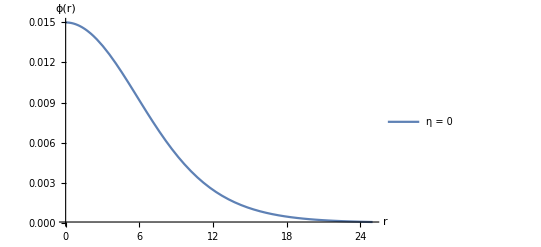

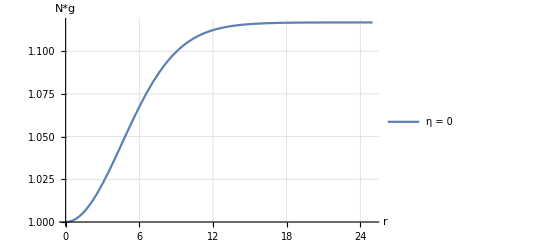

```mathematica
Plot[{Evaluate[φ[r]/.sB]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"}]

Plot[{Evaluate[NN[r]gg[r]/.sB]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N*g"},
GridLines->Automatic]
```

```mathematica
(*Check if the boundary conditions are satisface*)
```

```mathematica
Evaluate[NN[rMax]/.sB]*Evaluate[gg[rMax]/.sB]==1
```

{1.43097}==1

```mathematica
(* Calculated the constant A, that is use for the new boundary condition *)
```

```mathematica
A=NumberForm[Solve[C*Evaluate[NN[rMax]/.sB]*Evaluate[gg[rMax]/.sB]==1,C],{18,17}]
```

{{C→0.69882524882809780}}

#### Repeat the algorithm

```mathematica
SeidelBCList={};
AppendTo[SeidelBCList,{NN[rMin]==1*A[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];
```

```mathematica
w=w*A[[1,1,1,2]];
sB=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]
```

{{NN→                             -8
InterpolatingFunction[{{1. 10  , 30.}}, <>],gg→                             -8
InterpolatingFunction[{{1. 10  , 30.}}, <>],φ→                             -8
InterpolatingFunction[{{1. 10  , 30.}}, <>]}}

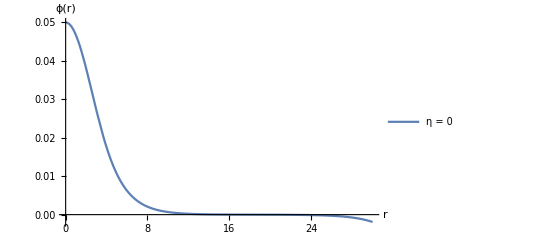

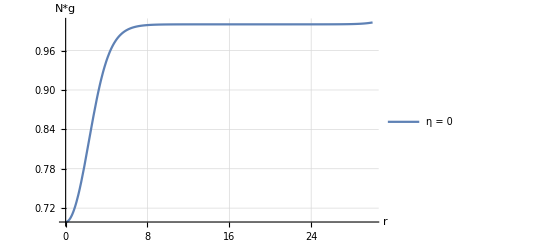

```mathematica
Plot[{Evaluate[φ[r]/.sB]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"}]

Plot[{Evaluate[NN[r]gg[r]/.sB]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N*g"},
GridLines->Automatic]
```

```mathematica
Evaluate[NN[rMax]/.sB]*Evaluate[gg[rMax]/.sB]==1
```

{1.00291}==1

```mathematica
w
```

0.847793

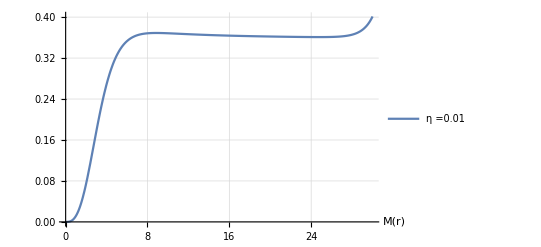

```mathematica
M[r_]:=1/2 r (1-1/gg[r]);
Plot[{Evaluate[M[r]/.sB]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η =0.01"},{0.85,0.6}],PlotRange->Full,
AxesLabel->{"M(r)"},
GridLines->Automatic]
```

#### Boson start

```mathematica
(*AppendTo[SeidelBCList,{NN[rMin]==1.,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] ==0, gg'[rMin] == 0}];*)
```

```mathematica
AppendTo[SeidelBCList,{NN[rMin]==1,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];
```

```mathematica
(*AppendTo[SeidelBCList,{NN[rMin]==0.7578344653876668,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] ==0, gg'[rMin] == 0}];*)
```

```mathematica
L1=1; η=0.01; α=1;
k=1/16/ π;mS=1;rMin=10^-8;ϕ0=0.05; w=1.219; rMax=14; 
sB=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]
```

```mathematica
Plot[{Evaluate[φ[r]/.sB]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"}]

(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.sB]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N(r)"},
GridLines->Automatic]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.sB]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.7}],PlotRange->Full,
AxesLabel->{"r","g(r)"},
GridLines->Automatic]

Plot[{Evaluate[NN[r]gg[r]/.sB]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.01","η = 0.1", "η = 0.3"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N*g"},
GridLines->Automatic]
```

```mathematica
Evaluate[NN[rMax]/.sB]
```

```mathematica
Evaluate[gg[rMax]/.sB]
```

```mathematica
NumberForm[Solve[A*Evaluate[NN[rMax]/.sB]*Evaluate[gg[rMax]/.sB]==1,A],{18,17}]
```

#### Checking ϕ0

```mathematica
L1=1; η=0; α=1;
k=1/16/ π;mS=1;rMin=10^-8;ϕ0=0.05; w=1.2189694 ; rMax=20; 
sB=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]

(*
L1=1; η=0.01; α=1;
k=1/16/ π;mS=1;rMin=10^-7;ϕ0=0.04; w=1.16448572184424; rMax=24.3; 
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]
*)

L1=1; η=0.1; α=1;
k=1/16/ π;mS=1;rMin=10^-8;ϕ0=0.05; w=1.221653322302503(*1.221653822302503000*); rMax=20; 
s2=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]

L1=1; η=0.5; α=1;
k=1/16/ π;mS=1;rMin=10^-8;ϕ0=0.05; w=1.235432379846161330; rMax=20; 
s3=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,WorkingPrecision->50,PrecisionGoal->30*),Method->{"EquationSimplification"->"Residual"}]
```

{{NN→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>],gg→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>],φ→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>]}}

{{NN→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>],gg→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>],φ→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>]}}

{{NN→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>],gg→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>],φ→                             -8
InterpolatingFunction[{{1. 10  , 20.}}, <>]}}

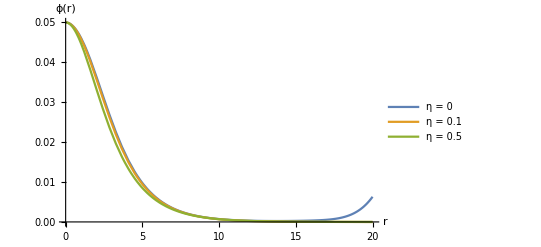

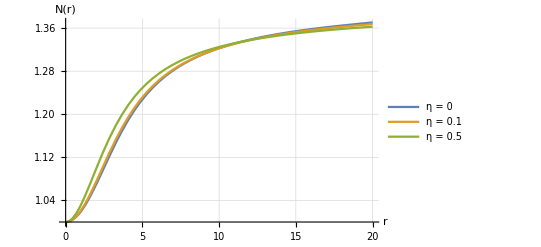

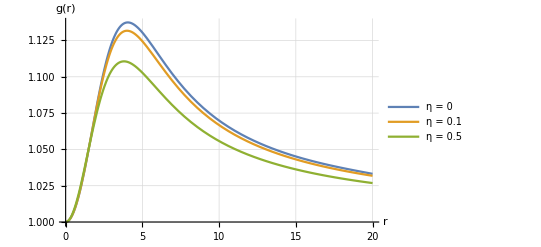

```mathematica
Plot[{Evaluate[φ[r]/.sB],(*Evaluate[φ[r]/.s1],*)Evaluate[φ[r]/.s2],Evaluate[φ[r]/.s3]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0","η = 0.1", "η = 0.5"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"}]

(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.sB],(*Evaluate[NN[r]/.s1],*)Evaluate[NN[r]/.s2],Evaluate[NN[r]/.s3]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0", "η = 0.1", "η = 0.5"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N(r)"},
GridLines->Automatic]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.sB],(*Evaluate[gg[r]/.s1],*)Evaluate[gg[r]/.s2],Evaluate[gg[r]/.s3]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η = 0","η = 0.1", "η = 0.5"},{0.85,0.7}],PlotRange->Full,
AxesLabel->{"r","g(r)"},
GridLines->Automatic]
```

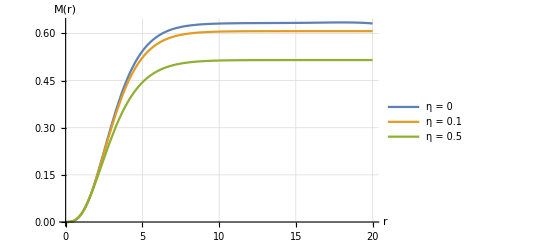

```mathematica
M[r_]:=1/2 r (1-1/gg[r]^2);

Plot[{Evaluate[M[r]/.sB](*,Evaluate[M[r]/.s1]*),Evaluate[M[r]/.s2],Evaluate[M[r]/.s3]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01"*),"η = 0.1", "η = 0.5"},{0.85,0.5}],PlotRange->Full,
AxesLabel->{"r","M(r)"},
GridLines->Automatic]
```

```mathematica
Eta1={{0.01,"1.034877595003519850",30},{0.015,1.054400754621342370,30},{0.02,1.075619047141195260,30},{0.03,1.124442586797270340,30},{0.04,1.184427493231167910,25},{0.042,1.198094352051323360,24},{0.044,"1.212387725311981250",22},{0.046,1.227320058123271870,19 },{0.048, 1.242910087527412020,19},{0.05,1.259088982231281420,19},{0.052,1.275627927330888900,19},{0.054, },{0.056,},{0.058,},{0.06,},{0.07,0.8238113468576481},{0.08,},{0.09,},{0.1,},{0.15,}};
```

```mathematica
{0.005,1.016762970255951990,99},{0.015,1.053447723388672000,30}
```

### Shooting

```mathematica
Subdivide[0.0032, 0.0052,5]
```

{0.0032,0.0036,0.004,0.0044,0.0048,0.0052}

```mathematica
eta03={{0.001,1.003273969640208350,100},{0.002,1.006588292246262580,99},{0.003,1.009940202510849830,99},{0.005,1.016762970255951990,99},{0.015,1.053447723388672000,30},{0.02,1.073574304580688000,30},{0.03,1.117992646992207000,30},{0.04,1.168950906586476000,30},{0.042,1.180049149401444000,30},{0.044,1.191479304473245000,30},{0.046,1.203255432745997000,30},{0.048,1.215391964651644000,27},{0.05,1.227904345312953000,30},{0.052,1.240808289952546000,30},{0.054,1.254119923742773000,30},{0.056,1.267856852990241000,30},{0.058,1.282036603689193000,22},{0.06,1.296677007475852000,30},{0.07,1.377422205836355000,21},{0.08,1.472049497589111000,12}};
```

```mathematica
ini
```

{0.001,0.002,0.00320000000000000015334955527635,0.00359999999999999990146770656452,0.00400000000000000008326672684689,0.00440000000000000026506574712926,0.00479999999999999957950302942322,0.00519999999999999976130204970559,0.00546666666666666654916806322717,0.00793333333333333390324781930758,0.0103999999999999995226040994112,0.0128666666666666668766838554916,0.0153333333333333324960401355952,0.0177999999999999998501198916756,0.0202666666666666689389231237328,0.0227333333333333310888324518828,0.02520000000000000017763568394,0.0276666666666666657969919640436,0.0301333333333333314163482441472,0.0326000000000000039745984281581,0.0350666666666666695939547082617,0.0375333333333333352133109883653,0.04,0.042,0.044,0.046,0.048,0.05,0.052,0.054,0.056,0.058,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.15,0.152,0.1592,0.16,0.1664,0.17,0.1736,0.1808,0.188,0.19,0.2,0.22,0.25,0.3}

```mathematica
Etam2={{0.015,1.052432290086502000,25},{0.02,1.072149053050892450,25}, {0.03,1.117065426352866810,25}, {0.04,1.173129288747914230,15}, {0.05,1.247924194428416700,15},{0.06,1.355370364587128000,15} ,{0.07,1.525012688428300000,12} ,{0.08,1.835501277315013130,10} ,{0.081,1.881629452180855410,8.5},{0.09,2.624200669364405890,7} };
```

```mathematica
1.052417474004111120413702646210350293010077961277169012453`30.
```

```mathematica
Dat={};
```

```mathematica
{0.00793333333333333390324781930758035741746425628662109375`30.,1.0270620626739372175991170353413084032725278239199563813585`30.,80.0699999999999,30,0.3,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0452331893360278159376986654537167344356200642107877991278`30.,50.070000000000014,30,0.3,0.01`30.}
```

```mathematica
{0.1000000000000000055511151231257827021181583404541015625`30.,1.568058291901689602300724247754550853345264240894827226558`30.,15.069999999999991,30,-0.3,0.01`30.}
```

```mathematica
Amp={0.11}; (* , 0.02, 0.03, 0.04, 0.05, 0.06, 0.07, 0.08*)
prec=30; (* precisión *)
Rmax=10;
Dat={};
η=-0.3;
α=1;k=1/16/ π;mS=1;L1=1;
```

```mathematica
rMin=SetPrecision[10^-2,prec];
rMax=SetPrecision[Rmax,prec];
UP=1.668782919016;
LOW=1.658782919016;(*0.9659.8*)
```

```mathematica
For[i=1,i<Length[Amp]+1,i++,
ϕ0=SetPrecision[Amp[[i]],prec]; 
ϕFlat=0;
rStart=rMin;(*rMin;*)
Clear[newStart];

(* start interval for search of omega, fixed by hand *)
omUP=SetPrecision[UP,prec];
omLOW=SetPrecision[LOW,prec];

While[ϕFlat==0,

If[newStart==1, 
newStart=0,
ϕFlat=1 ];

For[rTest =rStart+0.03(*rStart*), rTest <rMax+0.03,rTest+=0.1(*0.05*),
(*Print[rTest];*)
If[newStart==1,Break[]]; (* reiniciando rStart con el nuevo valor donde explotó *)

(*Print["rTest= ", rTest];*)
stop=0;

While[stop==0,

Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];ϕFlat=1;Break[],
SetPrecision[(omUP-omLOW)/2,prec]<10^-prec, (* Fijando la maxima precision *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];ϕFlat=1;Abort[]
           ];

w=SetPrecision[(omLOW+omUP)/2,prec];

(*Print[w];*)

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];
stop=1;

Do[
Which[Evaluate[φ[rp]/.s][[1]]>2ϕ0||Evaluate[φ[rp]/.s][[1]]>Evaluate[φ[rp-0.01]/.s][[1]],
stop=0;
Print["Pos"];
omLOW=SetPrecision[w,prec];
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[] (* Sale del ciclo Do *),
Evaluate[φ[rp]/.s][[1]]<-2ϕ0||Evaluate[φ[rp]/.s][[1]]<0,
stop=0;
Print["Neg"];
omUP=SetPrecision[w,prec];
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[](* Sale del ciclo Do *)
](* End Which*),{rp,rMin+0.03,rTest}
](* End Do *)
](* End While *)
 ](* End For that change the rTest value *)
];(* End While ϕFlat==0 *)
Print["Encontrado"];
Print[w];
AppendTo[Dat,{ϕ0,w,rTest,prec,η,rMin}];
](* End For that choose the ϕ0 value *);
```

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

General::stop: Further output of NDSolve::icfail will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
w
```

1.66878291901599995483707061794

```mathematica
Dat
```

{{0.0100000000000000002081668171172,1.03454719243435843695066921174,50.061,30,0.3,0.001}}

```mathematica
etam2={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032686979500788585962945356690317996683162583659206628079`30.,176.06099999999995,30,-2,0.001`30.},{0.01499999999999999944488848768742172978818416595458984375`30.,1.052417474004111120413702646210350293010077961277169012453`30.,35.070000000000014,30,-2,0.01`30.},{0.0200000000000000004163336342344337026588618755340576171875`30.,1.07214820500709030064187941296212677927572584553379900379`30.,35.06100000000003,30,-2,0.001`30.}}
```

Part::partd: Part specification AA⟦1⟧ is longer than depth of object.

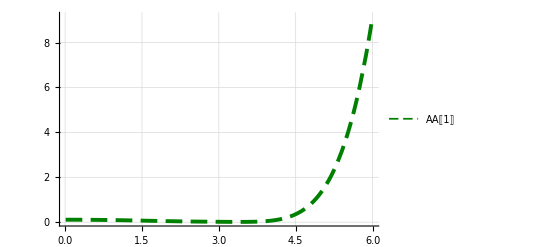

```mathematica
Plot[{Evaluate[φ[r]/.s]},{r,rMin,6},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

```mathematica
Eta03={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032747602904357822958525382597852130477539843953535922548`30.,150.06999999999954,30,0.3,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.006587190830295712342626299746756157263233944307168751162`30.,150.06999999999965,30,0.3,0.01`30.},{0.0032000000000000001533495552763497471460141241550445556641`30.,1.0106135330775051308337193616691758995562055419078988204955`30.,100.06999999999967,30,0.3,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.0119682068798921124133486603238272436932905635028540096008`30.,100.06999999999978,30,0.3,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0133293038760258846086468140797681462103989566478486313442`30.,100.06999999999972,30,0.3,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146967564929747512286294937377356381064430025087455473673`30.,80.06999999999961,30,0.3,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160706724574301490103591148793707563623070184230131271298`30.,80.06999999999955,30,0.3,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0174511269519148729364514180090273228767602661288221671552`30.,80.06999999999944,30,0.3,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.0183750368982948484340133007636535036404359122214605940388`30.,80.06999999999978,30,0.3,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0270620626739372175991170353413084032725278239199563813585`30.,80.0699999999999,30,0.3,0.01`30.},{0.0100000000000000002081668171172168513294309377670288085938`30.,1.0345471924343584369506692117375708544188167475080280003151`30.,50.06100000000006,30,0.3,0.001`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0452331893360278159376986654537167344356200642107877991278`30.,50.070000000000014,30,0.3,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0547417281509326771552611615751772670919479566618999566254`30.,50.070000000000014,30,0.3,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0645495993013036086336387560942795983083958695831124499407`30.,50.07000000000004,30,0.3,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0746712086700651575726740746753749142136670662247275356212`30.,50.07000000000004,30,0.3,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0851212609390880297287722869685471972013459277787175118159`30.,50.07000000000003,30,0.3,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0959154561720432335212371035209763692867756832564594175447`30.,30.070000000000086,30,0.3,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1070703551193921976418942252581703271814496905127694565301`30.,30.070000000000043,30,0.3,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.1186040462662582885349815928631109030514576825284162375959`30.,30.07000000000003,30,0.3,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1305349179069105638012714775273376389882941944882695067313`30.,30.070000000000043,30,0.3,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.1428831427916503201534346814971767605445479027011924911601`30.,30.070000000000057,30,0.3,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1556698224912977065016307346669602679022684213484705737934`30.,30.07000000000003,30,0.3,0.01`30.},{0.040000000000000000832667268468867405317723751068115234375`30.,1.1689171199979080032119261527870007701326835562703853003441`30.,30.070000000000014,30,0.3,0.01`30.},{0.042000000000000002609024107869117869995534420013427734375`30.,1.1800129928475641088474673691058090445615304360793544283767`30.,30.07000000000003,30,0.3,0.01`30.},{0.04399999999999999744648704336213995702564716339111328125`30.,1.1914403962458349959447498771508768665604517727419616146908`30.,30.070000000000057,30,0.3,0.01`30.},{0.04599999999999999922284388276239042170345783233642578125`30.,1.2032134956471430853168669822679894194442516499892908783418`30.,30.070000000000043,30,0.3,0.01`30.},{0.04800000000000000099920072216264088638126850128173828125`30.,1.2153470233010243679027886639019492347325775632141056433397`30.,30.070000000000014,30,0.3,0.01`30.},{0.05000000000000000277555756156289135105907917022705078125`30.,1.2278559583314948013805558426522668852956363086067580219955`30.,30.070000000000014,30,0.3,0.01`30.},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2407566070071718498545661063138107972881667880011991720547`30.,30.070000000000014,30,0.3,0.01`30.},{0.053999999999999999389377336456163902767002582550048828125`30.,1.2540651459427390675364701004624271833808006094226708408704`30.,30.070000000000014,30,0.3,0.01`30.},{0.056000000000000001165734175856414367444813251495361328125`30.,1.2677985898558739538332765574039556632092672783922480933471`30.,30.070000000000014,30,0.3,0.01`30.},{0.058000000000000002942091015256664832122623920440673828125`30.,1.2819747100665400163858990186123352572899140050258193779936`30.,30.070000000000014,30,0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2966115045798694441587962499183915647859786794512963160083`30.,30.07000000000003,30,0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2966115874051752575499979156944799614751963526555253479636`30.,20.070000000000014,30,0.3,0.01`30.},{0.070000000000000006661338147750939242541790008544921875`30.,1.3773398393006772073807982193090534048461327238126206049275`30.,20.07000000000003,30,0.3,0.01`30.},{0.08000000000000000166533453693773481063544750213623046875`30.,1.4719135834424746974380579827404594012894102799158426753109`30.,20.070000000000057,30,0.3,0.01`30.}};
```

```mathematica
Etam03={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032730022983853821303561268400154449192330540462007821894`30.,176,30,-0.3,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.0065799461494501541819545258672931154925138382964240697206`30.,143.06999999999994,30,-0.3,0.01`30.},{0.0032000000000000001533495552763497471460141241550445556641`30.,1.0105943416790243250634535468193862502128431243530754541181`30.,100.0699999999999,30,-0.3,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.0119435729045454536876212778596582299573849385228739913253`30.,100.06999999999961,30,-0.3,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0132984695633800182415892718524422714436652423088313236591`30.,80.06999999999967,30,-0.3,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146590437860911903802235097985129008338724016213804323155`30.,80.06999999999915,30,-0.3,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160253253877096582115357548591261857814275199545917458729`30.,80.06999999999984,30,-0.3,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0173973026377315444471279362823125258980993434747326366936`30.,80.06999999999967,30,-0.3,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.0183150153769131991571518995362149003828917859756419496397`30.,60.07000000000004,30,-0.3,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0269263755618292145423183946289692435686159289330276139799`30.,60.07000000000006,30,-0.3,0.01`30.},{0.010399999999999999522604099411182687617838382720947265625`30.,1.0357611351366596528899535652699588110204099697561632096197`30.,60.070000000000086,30,-0.3,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0448244655178519680863143082528859157866491006846278098122`30.,40.07000000000006,30,-0.3,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0541220290213564021949714955210224784050680990868943946814`30.,40.070000000000086,30,-0.3,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0636597256309179944411342786339009210780830398717868154977`30.,40.07000000000003,30,-0.3,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0734435644283601774482809738414173414128302822511850722735`30.,40.070000000000014,30,-0.3,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0834785123089794941487036756039294065246864270529506062805`30.,30.070000000000057,30,-0.3,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0937719913321628699577013704919345685229691613831570173172`30.,30.070000000000043,30,-0.3,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1043295288862257261817553792071962775007266983682644300298`30.,30.07000000000003,30,-0.3,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.1151582315406098693728822748887597290740176703615252730931`30.,30.070000000000043,30,-0.3,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1262643062990049786714509631897150308062350600512233133244`30.,30.070000000000086,30,-0.3,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.1376546774953322837776033245204343009113739124807627611112`30.,30.070000000000043,30,-0.3,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1493366975098440465531281552752161605622573266044246685014`30.,30.070000000000014,30,-0.3,0.01`30.},{0.040000000000000000832667268468867405317723751068115234375`30.,1.1613171191571093532766674680202811916996775593884803305847`30.,25.070000000000043,30,-0.3,0.01`30.},{0.042000000000000002609024107869117869995534420013427734375`30.,1.1712552203463037939013152569966505293455323221483686822163`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04399999999999999744648704336213995702564716339111328125`30.,1.1813986808106753382131971807855089525645575441402093955292`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04599999999999999922284388276239042170345783233642578125`30.,1.1917514159436011485560156122020326900257934877286827352648`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04800000000000000099920072216264088638126850128173828125`30.,1.202317477866481081831506975175578727589897694281680023029`30.,25.070000000000057,30,-0.3,0.01`30.},{0.05000000000000000277555756156289135105907917022705078125`30.,1.2131016365228341413710864619849530263735184199339506289635`30.,25.070000000000014,30,-0.3,0.01`30.},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2241078555524592470578757532998621410674823273464404337253`30.,20.070000000000014,30,-0.3,0.01`30.},{0.053999999999999999389377336456163902767002582550048828125`30.,1.2353408700883620253504352919523043769256754694902070089369`30.,20.070000000000014,30,-0.3,0.01`30.},{0.056000000000000001165734175856414367444813251495361328125`30.,1.2468063193200097260379598183440923077908036205538737639122`30.,20.070000000000014,30,-0.3,0.01`30.},{0.058000000000000002942091015256664832122623920440673828125`30.,1.2585051522457477882765577651895613929402408155257925063127`30.,20.070000000000057,30,-0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2704460851777564870592641148577739837575362557779996688086`30.,20.070000000000014,30,-0.3,0.01`30.},{0.070000000000000006661338147750939242541790008544921875`30.,1.3339336275418824559937050199198665006870666414577333999835`30.,20.070000000000043,30,-0.3,0.01`30.},{0.08000000000000000166533453693773481063544750213623046875`30.,1.4042096353786290789248800359620966596130197518832230960207`30.,20.07000000000003,30,-0.3,0.01`30.},{0.0899999999999999966693309261245303787291049957275390625`30.,1.4819868621430601038800347003539114991415719914690908851582`30.,15.069999999999991,30,-0.3,0.01`30.},{0.1000000000000000055511151231257827021181583404541015625`30.,1.568058291901689602300724247754550853345264240894827226558`30.,15.069999999999991,30,-0.3,0.01`30.},{0.11,1.6636919016,10,30,-0.3,0.001},{0.12,1.769419016,10,30,-0.3,0.001}};
```

```mathematica
Etam03={{0.015,1.0528621673583980,30,30,-0.3,0.01`30.},{0.02,1.0723885893821720,30,30,30,-0.3,10^-3},{0.03,1.1145928651094440,30,30,30,-0.3,10^-3},{0.04,1.1613612586750880,30,30,30,-0.3,10^-3},{0.042,1.1713035509047010,25,30,30,-0.3,10^-3},{0.044,1.1814513386399140,30,30,30,-0.3,10^-3},{0.046,1.1918086057616720,30,30,30,-0.3,10^-3},{0.048,1.2023797700315790,30,30,30,-0.3,10^-3},{0.05,1.2131691131351870,30,30,30,-0.3,10^-3},{0.052,1.224180970558401000,30,30,30,-0.3,10^-3},{0.054,1.2354198299260930,30,30,30,-0.3,10^-3},{0.056,1.246890453211968000,30,30,30,-0.3,10^-3},{0.058,1.258597242059905000,22,30,30,-0.3,10^-3},{0.06,1.2705452417886480,30,30,30,-0.3,10^-3},{0.07,1.334076062600186000,18,30,30,-0.3,10^-3},{0.08,1.404409375520368000,17,30,30,-0.3,10^-3},{0.09,1.482261297866646000,18,30,30,-0.3,10^-3},{0.1,1.568426066103807000,20,30,30,-0.3,10^-3}};
```

```mathematica
Dat=Eta03;
```

```mathematica
Table[
AA=Dat[[i]];
prec=AA[[4]];
η= AA[[5]]; 
α=1;k=1/16/ π;mS=1;L1=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec];
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];

(*s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];*)

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; (*φ*)

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[Dat]}](*Length[Dat]*)
```

#### Shooting

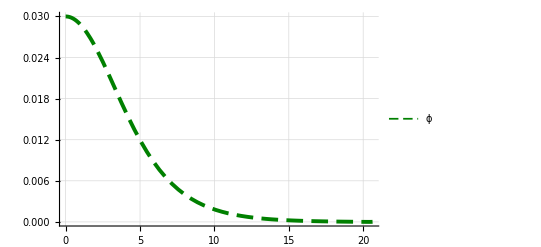

{0.591692}

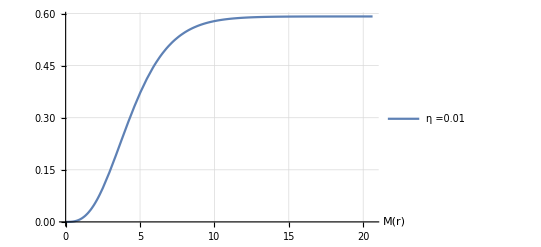

```mathematica
L1=1; η=0;ϕ0=0.03; α=1;
k=1/16/ π;mS=1;rMin=10^-10; rMax=20;
ϕFlat=0;
r0=1;
rGoal = rMax+2;
(* start interval for search of omega, fixed by hand *)
omLOW=.559296185798055030;
omUP   =2.00559296185798055030;

(* switch off some error messages *)
Off[NDSolve::ndsz];
 Off[NDSolve::icfail]; 
Off[InterpolatingFunction::dmval];

While[ϕFlat==0,
(*
Print["Memory Occupied: ", MemoryInUse[]];
*)
(* Controlando memoria y precision en la frecuencia *)
Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];Break[],
(omUP-omLOW)/2<10^-15, (* Fijando la maxima precision en w a 10^-15 *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];Break[]
           ];
(*

Print["omLOW = ", NumberForm[omLOW,{18,19}]];
Print["omUP  = ", NumberForm[omUP,{18,19}]];
Print["Δω = ",NumberForm[(omUP-omLOW)/2,{18,19}]];
*)
(*w=(omLOW+omUP)/2;*)
 w=RandomReal[{omLOW,omUP},WorkingPrecision->18];

(*
Print["ω = ",NumberForm[w,{19,18}]," r = ",rTest];
Print["\n"];
*)
s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

(* shotting *)
For[rTest =r0, rTest <rGoal,rTest+=0.01,
     (*     Print[ "rTest = ", rTest, "   ϕ[rTest] = ", Evaluate[φ[rTest]/.s][[1]] ];*)
Which[Evaluate[φ[1]/.s][[1]]<10^-5,
(*Print[" --> Problem with boundary conditions change"];*)
omLOW=omLOW+1*10^-4;
Break[],
Evaluate[φ[1]/.s][[1]]>10^5,
(*Print[" --> Problem with boundary conditions change"];*)
omLOW=omLOW+1*10^-4;
Break[],
Evaluate[φ[rTest]/.s][[1]]<0,
Print["rTest = ", rTest, " --> ϕ negative --> decreasing Upper Bound of omega", "ω = ",NumberForm[w,{19,18}]];
omUP=w;
(*Print["eqϕ ",SeidelEqsList[[1,1]]];
ϕFlat=1;*)
Break[],
Evaluate[φ[rTest]/.s][[1]]>Evaluate[φ[rTest-1]/.s][[1]]&&rTest>1 ,
Print["rTest = ", rTest, " -> ϕ Local Minimum -> increasing Lower Bound of omega", "ω = ",NumberForm[w,{19,18}]];
omLOW=w;
(*Print["eqϕ ",SeidelEqsList[[1,1]]];
ϕFlat=1;*)
Break[],
rTest> rGoal-1,
Print["rTest = ", rTest, " --> rGoal reached"];
ϕFlat=1;
Break[],
Evaluate[φ[rTest]/.s][[1]]==1,
(*Print[" --> Problem with boundary conditions", "ω = ",NumberForm[w,{19,18}]];*)
omLOW=omLOW+1*10^-4;
Break[]
          ](*Which*)   
     ](* FOR *)
 ](* While *)
(* Resultados *)
Speak["o mega is calculated"]

Print["ω = ",NumberForm[w,{19,18}]];
Print["Δω = ",NumberForm[(omUP-omLOW)/2,{19,18}]];

(* Plot the scalar field *)
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rTest},
Background->White,PlotLegends->{"ϕ"},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
M[r_]:=1/2 r (1-1/gg[r]^2);
Mtot=Evaluate[M[rTest]/.s]
(*Mrel[r_]:=M[r]/Mtot;*)
Plot[{Evaluate[M[r]/.s]},
{r,rMin,rTest},Background->White,PlotLegends->Placed[{"η =0.01"},{0.85,0.6}],PlotRange->Full,
AxesLabel->{"M(r)"},
GridLines->Automatic]
```

-Graphics-

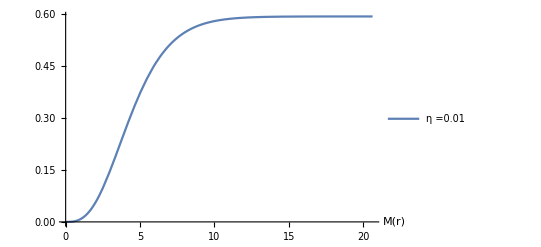

```mathematica
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rTest},
Background->White,PlotLegends->{"ϕ"},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]

Plot[{Evaluate[M[r]/.s]},
{r,rMin,rTest},Background->White,PlotLegends->Placed[{"η =0.01"},{0.85,0.6}],PlotRange->Full,
AxesLabel->{"M(r)"}]
```

```mathematica
Funcsigma={};
Do[AppendTo[Funcsigma,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

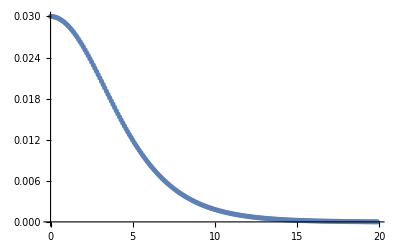

```mathematica
ListPlot[Funcsigma]
```

```mathematica
Export["Funcsigma.dat",Funcsigma]
```

Funcsigma.dat

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

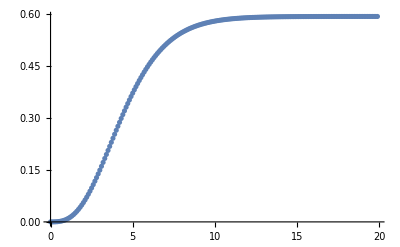

```mathematica
ListPlot[Funcg]
```

```mathematica
Export["M_KG.dat",Funcg]
```

M_KG.dat

#### Test

```mathematica
(*0.122 1.829419016, 1.83266016*)
```

```mathematica
{0.05,1.219018571342151000,30}
```

```mathematica
{0.12,1.769419016,10,30,-0.3,0.001}
```

```mathematica
{0.125,1.8264646898,10,30,-0.3,0.0001}
```

```mathematica
L1=1; η=-0.3;ϕ0=0.13; α=1; (* 1.58582919016*)
k=1/16/ π;mS=1;rMin=10^-3(*10^-3*); w=1.8808646898; (*1.832646898*); rMax=10;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

```mathematica
a=SeidelEqsList[[1]]/.(SeidelBCList[[1]]/.rMin-> r/.Equal-> Rule)//Simplify
```

{φ''[r]==(-0.205343+0.459895 r-0.303995 r^2+(-0.346796+0.793785 r-0.294595 r^2) gg'[r]+0.26104 r NN''[r])/(0.192398-0.601682 r+1. r^2),0.766168/r+1. r==2.03644,gg'[r]==0.2962/r-0.898405 r-5.71963 φ''[r]}

```mathematica
NSolve[a[[2]],r]
```

{{r→1.53842},{r→0.498024}}

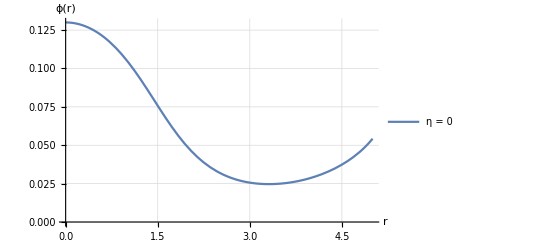

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,5},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

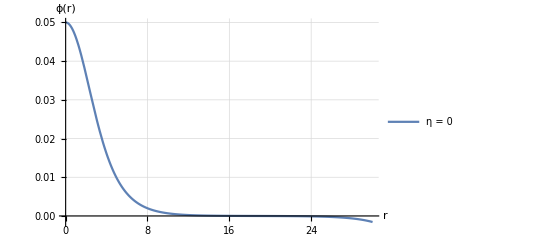

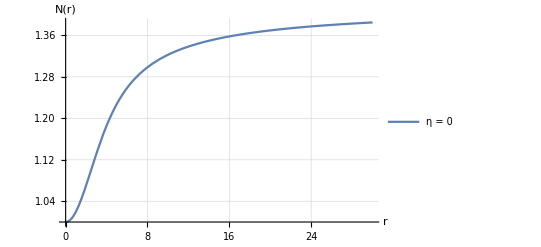

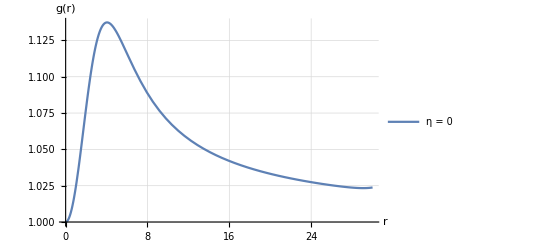

```mathematica
(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.s1]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N(r)"},
GridLines->Automatic]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.7}],PlotRange->Full,
AxesLabel->{"r","g(r)"},
GridLines->Automatic]
```

```mathematica
Evaluate[φ[rMax]/.s1]
```

{0.000651284}

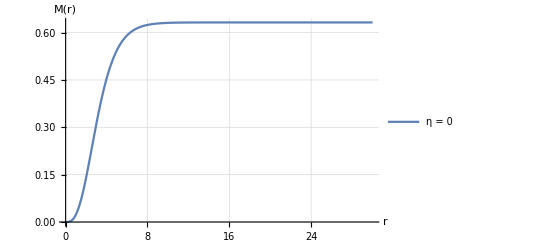

```mathematica
M[r_]:=1/2 r (1-1/gg[r]^2);
(*Mtot=Evaluate[M[rMax]/.s2]*)
(*Mrel[r_]:=M[r]/Mtot;*)
Plot[{Evaluate[M[r]/.s1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.5}],PlotRange->Full,
AxesLabel->{"r","M(r)"},
GridLines->Automatic]
```

```mathematica
Evaluate[M[10]/.s1]-Evaluate[M[9]/.s1]/1
```

{-0.0089798}

```mathematica
ini={};
Do[AppendTo[ini,Bs[[i,1]]],{i,1,Length[Bs]}]
```

```mathematica
ini
```

#### Shooting M

```mathematica
Bs={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032736825266425024546711200243289808219829642490431642279`30.,200.07000000000227,30,0,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.0065835949573696846177350275907531973318828825330502424441`30.,190.0700000000034,30,0,0.01`30.},
(*{0.0030000000000000000624500451351650553988292813301086425781`30.,1.0099321063764611044831211129554904282201732712564989924431`30.,60.06999999999989,30,0,0.01`30.},*){0.0032000000000000001533495552763497471460141241550445556641`30.,1.0106016081544170002223179530436890442542455237351362029585`30.,60.069999999999716,30,0,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.011954987515376924431307884387624283415146181352994858571`30.,60.06999999999983,30,0,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0133129876708166055894180393211253105701470308974698752991`30.,60.06999999999994,30,0,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146771488855626293463551590407140550506148030107667068478`30.,60.0699999999996,30,0,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160472144488105647605014533469701953013217092525177775997`30.,60.06999999999983,30,0,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0174231843605604118318569222398937313222677496227230875547`30.,60.069999999999716,30,0,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.018344006016054199414870367560587149924344885221216827631`30.,60.06999999999949,30,0,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0269905817532166681635218399975813079183506459912678110413`30.,60.06999999999966,30,0,0.01`30.},{0.010399999999999999522604099411182687617838382720947265625`30.,1.035877489321508490142804696249468742602628523741259414237`30.,60.06999999999926,30,0,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0450121304801593362174921948526086434039261176265345198999`30.,60.06999999999977,30,0,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0544028365789439100604072456968878003943835446661742016872`30.,60.06999999999977,30,0,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0640581996429191519093299377975697251357036014120390453319`30.,60.06999999999989,30,0,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0739868036134406465836717132219519480499393153800694440886`30.,60.06999999999994,30,0,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0841977627770874465590274159289713584768273016454656708576`30.,40.06999999999989,30,0,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0947006056786406716104757733107748507119282202911661427939`30.,40.06999999999994,30,0,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1055050253841343332553983559482949272163299758359577149797`30.,40.06999999999994,30,0,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.116621675308330270834470692444677922878711745038039017396`30.,40.06999999999989,30,0,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1280614286283593470397314504385750221800343992547902878813`30.,40.06999999999989,30,0,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.139835246169145591954234162767783603568587105141681801049`30.,40.06999999999989,30,0,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1519550542739285921023498946308235325655241567194072317374`30.,40.06999999999994,30,0,0.01`30.},{0.04,1.16447077028579,20.,30.,0.,1.*^-8},{0.042,1.174863039742705,20.,30.,0.,1.*^-8},{0.044,1.185506651020017,30.,30.,0.,1.*^-8},{0.046,1.196408378494969,30.,30.,0.,1.*^-8},{0.048,1.207576510035849,20.,30.,0.,1.*^-8},{0.05,1.219018571342151,20.,30.,0.,1.*^-8},{0.052,1.230742623941348,20.,30.,0.,1.*^-8},{0.054,1.242757501645907,20.,30.,0.,1.*^-8},{0.056,1.255071652560727,20.,30.,0.,1.*^-8},{0.058,1.267694320796101,18.,30.,0.,1.*^-8},{0.06,1.28063495884173,15.,30.,0.,1.*^-8},{0.07,1.350463702269447,30.,30.,0.,1.*^-8},{0.08,1.429880054976501,23.,14.,0.,1.*^-8},{0.09,1.520545101912098,14.,30.,0.,1.*^-8},{0.1,1.624469884859628,14.,30.,0.,1.*^-8},{0.11,1.7441016166994885,20.,30.,0.,1.*^-8},{0.13,2.0430621612059983,13.,30.,0.,1.*^-8},{0.15,2.449966765699886,13.,30.,0.,1.*^-8},{0.152,2.4958022244291476,18.,30.,0.,0.01},{0.1592,2.68250370388174,20.070000000000014,30.,0.,0.01},{0.16,2.7080677018789943,19.,30.,0.,1.*^-8},{0.1664,2.892505947790201,20.070000000000014,30.,0.,0.01},{0.17,3.012458355733277,19.,30.,0.,1.*^-8},{0.1736,3.1289332343242386,20.070000000000014,30.,0.,0.01},{0.1808,3.3952169283467635,20.070000000000014,30.,0.,0.01},{0.188,3.695071314017931,20.070000000000014,30.,0.,0.01},{0.19,3.7975050018636938,14.,30.,0.,1.*^-8},{0.2,4.300155639648437,13.1,30.,0.,1.*^-8},{0.22,5.590762832128472,13.,30.,0.,1.*^-8},{0.25,8.503837558382656,14.,30.,0.,1.*^-8},{0.3,18.2904052734375,12.,30.,0.,1.*^-8}};
```

```mathematica
Etam03={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032730022983853821303561268400154449192330540462007821894`30.,176,30,-0.3,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.0065799461494501541819545258672931154925138382964240697206`30.,143.06999999999994,30,-0.3,0.01`30.},{0.0032000000000000001533495552763497471460141241550445556641`30.,1.0105943416790243250634535468193862502128431243530754541181`30.,100.0699999999999,30,-0.3,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.0119435729045454536876212778596582299573849385228739913253`30.,100.06999999999961,30,-0.3,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0132984695633800182415892718524422714436652423088313236591`30.,80.06999999999967,30,-0.3,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146590437860911903802235097985129008338724016213804323155`30.,80.06999999999915,30,-0.3,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160253253877096582115357548591261857814275199545917458729`30.,80.06999999999984,30,-0.3,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0173973026377315444471279362823125258980993434747326366936`30.,80.06999999999967,30,-0.3,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.0183150153769131991571518995362149003828917859756419496397`30.,60.07000000000004,30,-0.3,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0269263755618292145423183946289692435686159289330276139799`30.,60.07000000000006,30,-0.3,0.01`30.},{0.010399999999999999522604099411182687617838382720947265625`30.,1.0357611351366596528899535652699588110204099697561632096197`30.,60.070000000000086,30,-0.3,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0448244655178519680863143082528859157866491006846278098122`30.,40.07000000000006,30,-0.3,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0541220290213564021949714955210224784050680990868943946814`30.,40.070000000000086,30,-0.3,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0636597256309179944411342786339009210780830398717868154977`30.,40.07000000000003,30,-0.3,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0734435644283601774482809738414173414128302822511850722735`30.,40.070000000000014,30,-0.3,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0834785123089794941487036756039294065246864270529506062805`30.,30.070000000000057,30,-0.3,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0937719913321628699577013704919345685229691613831570173172`30.,30.070000000000043,30,-0.3,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1043295288862257261817553792071962775007266983682644300298`30.,30.07000000000003,30,-0.3,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.1151582315406098693728822748887597290740176703615252730931`30.,30.070000000000043,30,-0.3,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1262643062990049786714509631897150308062350600512233133244`30.,30.070000000000086,30,-0.3,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.1376546774953322837776033245204343009113739124807627611112`30.,30.070000000000043,30,-0.3,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1493366975098440465531281552752161605622573266044246685014`30.,30.070000000000014,30,-0.3,0.01`30.},{0.040000000000000000832667268468867405317723751068115234375`30.,1.1613171191571093532766674680202811916996775593884803305847`30.,25.070000000000043,30,-0.3,0.01`30.},{0.042000000000000002609024107869117869995534420013427734375`30.,1.1712552203463037939013152569966505293455323221483686822163`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04399999999999999744648704336213995702564716339111328125`30.,1.1813986808106753382131971807855089525645575441402093955292`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04599999999999999922284388276239042170345783233642578125`30.,1.1917514159436011485560156122020326900257934877286827352648`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04800000000000000099920072216264088638126850128173828125`30.,1.202317477866481081831506975175578727589897694281680023029`30.,25.070000000000057,30,-0.3,0.01`30.},{0.05000000000000000277555756156289135105907917022705078125`30.,1.2131016365228341413710864619849530263735184199339506289635`30.,25.070000000000014,30,-0.3,0.01`30.},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2241078555524592470578757532998621410674823273464404337253`30.,20.070000000000014,30,-0.3,0.01`30.},{0.053999999999999999389377336456163902767002582550048828125`30.,1.2353408700883620253504352919523043769256754694902070089369`30.,20.070000000000014,30,-0.3,0.01`30.},{0.056000000000000001165734175856414367444813251495361328125`30.,1.2468063193200097260379598183440923077908036205538737639122`30.,20.070000000000014,30,-0.3,0.01`30.},{0.058000000000000002942091015256664832122623920440673828125`30.,1.2585051522457477882765577651895613929402408155257925063127`30.,20.070000000000057,30,-0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2704460851777564870592641148577739837575362557779996688086`30.,20.070000000000014,30,-0.3,0.01`30.},{0.070000000000000006661338147750939242541790008544921875`30.,1.3339336275418824559937050199198665006870666414577333999835`30.,20.070000000000043,30,-0.3,0.01`30.},{0.08000000000000000166533453693773481063544750213623046875`30.,1.4042096353786290789248800359620966596130197518832230960207`30.,20.07000000000003,30,-0.3,0.01`30.},{0.0899999999999999966693309261245303787291049957275390625`30.,1.4819868621430601038800347003539114991415719914690908851582`30.,15.069999999999991,30,-0.3,0.01`30.},{0.1000000000000000055511151231257827021181583404541015625`30.,1.568058291901689602300724247754550853345264240894827226558`30.,15.069999999999991,30,-0.3,0.01`30.}};
```

```mathematica
Eta03={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032747602904357822958525382597852130477539843953535922548`30.,150.06999999999954,30,0.3,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.006587190830295712342626299746756157263233944307168751162`30.,150.06999999999965,30,0.3,0.01`30.},{0.0032000000000000001533495552763497471460141241550445556641`30.,1.0106135330775051308337193616691758995562055419078988204955`30.,100.06999999999967,30,0.3,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.0119682068798921124133486603238272436932905635028540096008`30.,100.06999999999978,30,0.3,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0133293038760258846086468140797681462103989566478486313442`30.,100.06999999999972,30,0.3,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146967564929747512286294937377356381064430025087455473673`30.,80.06999999999961,30,0.3,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160706724574301490103591148793707563623070184230131271298`30.,80.06999999999955,30,0.3,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0174511269519148729364514180090273228767602661288221671552`30.,80.06999999999944,30,0.3,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.0183750368982948484340133007636535036404359122214605940388`30.,80.06999999999978,30,0.3,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0270620626739372175991170353413084032725278239199563813585`30.,80.0699999999999,30,0.3,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0452331893360278159376986654537167344356200642107877991278`30.,50.070000000000014,30,0.3,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0547417281509326771552611615751772670919479566618999566254`30.,50.070000000000014,30,0.3,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0645495993013036086336387560942795983083958695831124499407`30.,50.07000000000004,30,0.3,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0746712086700651575726740746753749142136670662247275356212`30.,50.07000000000004,30,0.3,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0851212609390880297287722869685471972013459277787175118159`30.,50.07000000000003,30,0.3,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0959154561720432335212371035209763692867756832564594175447`30.,30.070000000000086,30,0.3,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1070703551193921976418942252581703271814496905127694565301`30.,30.070000000000043,30,0.3,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.1186040462662582885349815928631109030514576825284162375959`30.,30.07000000000003,30,0.3,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1305349179069105638012714775273376389882941944882695067313`30.,30.070000000000043,30,0.3,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.1428831427916503201534346814971767605445479027011924911601`30.,30.070000000000057,30,0.3,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1556698224912977065016307346669602679022684213484705737934`30.,30.07000000000003,30,0.3,0.01`30.},{0.040000000000000000832667268468867405317723751068115234375`30.,1.1689171199979080032119261527870007701326835562703853003441`30.,30.070000000000014,30,0.3,0.01`30.},{0.042000000000000002609024107869117869995534420013427734375`30.,1.1800129928475641088474673691058090445615304360793544283767`30.,30.07000000000003,30,0.3,0.01`30.},{0.04399999999999999744648704336213995702564716339111328125`30.,1.1914403962458349959447498771508768665604517727419616146908`30.,30.070000000000057,30,0.3,0.01`30.},{0.04599999999999999922284388276239042170345783233642578125`30.,1.2032134956471430853168669822679894194442516499892908783418`30.,30.070000000000043,30,0.3,0.01`30.},{0.04800000000000000099920072216264088638126850128173828125`30.,1.2153470233010243679027886639019492347325775632141056433397`30.,30.070000000000014,30,0.3,0.01`30.},{0.05000000000000000277555756156289135105907917022705078125`30.,1.2278559583314948013805558426522668852956363086067580219955`30.,30.070000000000014,30,0.3,0.01`30.},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2407566070071718498545661063138107972881667880011991720547`30.,30.070000000000014,30,0.3,0.01`30.},{0.053999999999999999389377336456163902767002582550048828125`30.,1.2540651459427390675364701004624271833808006094226708408704`30.,30.070000000000014,30,0.3,0.01`30.},{0.056000000000000001165734175856414367444813251495361328125`30.,1.2677985898558739538332765574039556632092672783922480933471`30.,30.070000000000014,30,0.3,0.01`30.},{0.058000000000000002942091015256664832122623920440673828125`30.,1.2819747100665400163858990186123352572899140050258193779936`30.,30.070000000000014,30,0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2966115045798694441587962499183915647859786794512963160083`30.,30.07000000000003,30,0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2966115874051752575499979156944799614751963526555253479636`30.,20.070000000000014,30,0.3,0.01`30.},{0.070000000000000006661338147750939242541790008544921875`30.,1.3773398393006772073807982193090534048461327238126206049275`30.,20.07000000000003,30,0.3,0.01`30.},{0.08000000000000000166533453693773481063544750213623046875`30.,1.4719135834424746974380579827404594012894102799158426753109`30.,20.070000000000057,30,0.3,0.01`30.}};
```

```mathematica
Length[Bs]
```

53

```mathematica
Bs[[13]]
```

{{53.4777,0.137603},{37.6708,0.193068},{29.6458,0.241901},{27.9135,0.255777},{26.4405,0.268763},{25.1721,0.280994},{24.0637,0.292562},{23.0862,0.303558},{22.4935,0.310594},{18.5016,0.367004},{16.0126,0.412222},{14.2652,0.449845},{12.9497,0.481864},{11.9108,0.509499},{11.0618,0.533581},{10.351,0.55473},{9.74309,0.573365},{9.2152,0.589857},{8.75099,0.604484},{8.33832,0.617473},{7.96786,0.629009},{7.63277,0.639251},{7.32753,0.648335},{7.09897,0.654931},{6.88539,0.660899},{6.68505,0.666284},{6.49658,0.671133},{6.31881,0.675482},{6.15086,0.679374},{5.9916,0.682834},{5.84031,0.685892},{5.69644,0.688584},{5.55908,0.690921},{4.95656,0.698185},{4.46041,0.699594},{4.03987,0.696742},{3.67493,0.690746}}

{{0.00100000000000000002081668171172,0.137603},{0.00200000000000000004163336342344,0.193068},{0.00320000000000000015334955527635,0.241901},{0.00359999999999999990146770656452,0.255777},{0.00400000000000000008326672684689,0.268763},{0.00440000000000000026506574712926,0.280994},{0.00479999999999999957950302942322,0.292562},{0.00519999999999999976130204970559,0.303558},{0.00546666666666666654916806322717,0.310594},{0.00793333333333333390324781930758,0.367004},{0.0103999999999999995226040994112,0.412222},{0.0128666666666666668766838554916,0.449845},{0.0153333333333333324960401355952,0.481864},{0.0177999999999999998501198916756,0.509499},{0.0202666666666666689389231237328,0.533581},{0.0227333333333333310888324518828,0.55473},{0.02520000000000000017763568394,0.573365},{0.0276666666666666657969919640436,0.589857},{0.0301333333333333314163482441472,0.604484},{0.0326000000000000039745984281581,0.617473},{0.0350666666666666695939547082617,0.629009},{0.0375333333333333352133109883653,0.639251},{0.0400000000000000008326672684689,0.648335},{0.0420000000000000026090241078691,0.654931},{0.0439999999999999974464870433621,0.660899},{0.0459999999999999992228438827624,0.666284},{0.0480000000000000009992007221626,0.671133},{0.0500000000000000027755575615629,0.675482},{0.0519999999999999976130204970559,0.679374},{0.0539999999999999993893773364562,0.682834},{0.0560000000000000011657341758564,0.685892},{0.0580000000000000029420910152567,0.688584},{0.0599999999999999977795539507497,0.690921},{0.0700000000000000066613381477509,0.698185},{0.0800000000000000016653345369377,0.699594},{0.0899999999999999966693309261245,0.696742},{0.100000000000000005551115123126,0.690746}}

{{0.99654,0.137603},{0.9931,0.193068},{0.988997,0.241901},{0.987636,0.255777},{0.986277,0.268763},{0.984922,0.280994},{0.98357,0.292562},{0.98222,0.303558},{0.981323,0.310594},{0.973082,0.367004},{0.964954,0.412222},{0.956937,0.449845},{0.949028,0.481864},{0.941225,0.509499},{0.933525,0.533581},{0.925924,0.55473},{0.918424,0.573365},{0.911018,0.589857},{0.903704,0.604484},{0.89648,0.617473},{0.889343,0.629009},{0.88229,0.639251},{0.875318,0.648335},{0.869723,0.654931},{0.864177,0.660899},{0.858679,0.666284},{0.853227,0.671133},{0.847819,0.675482},{0.842454,0.679374},{0.83713,0.682834},{0.831845,0.685892},{0.826597,0.688584},{0.821385,0.690921},{0.795781,0.698185},{0.770756,0.699594},{0.746033,0.696742},{0.721312,0.690746}}

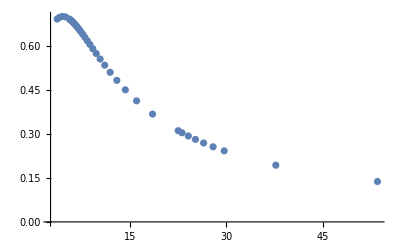

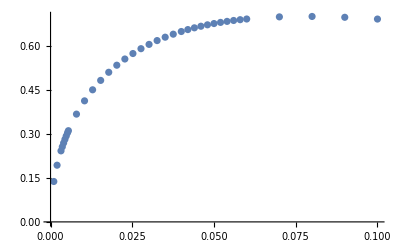

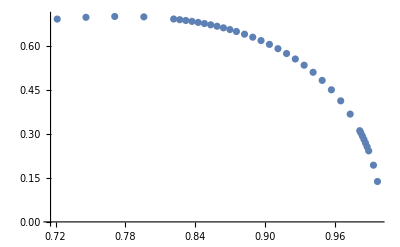

```mathematica
mvsr={};
phivswf={};
wfvsm={};
stop2=0;

For[j=1,j<Length[Etam03]+1,j++,
Print[j];

AA=Etam03[[j]];
prec=AA[[4]];
η= AA[[5]]; 
α=1;k=1/16/ π;mS=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec];
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];

Clear[s,M95, M];

If[stop2≠0,Break[]]; (*Para cuando una frecuencia no es suficientemente pequeña*)

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]; 

M95=0.95M[rMax][[1]];

(* comprobando ϕ pequeño *)
If[Evaluate[φ[rMax]/.s][[1]]<4*10^-3,Print["cumple con ϕ<10^-3"],Print["No cumple con ϕ<10^-3"]; Break[]];

(* calculando radio *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];

Print[rad];
Print["masa95 = ", M95];

(* calculando frecuencia*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];

AppendTo[mvsr,{rad[[2]],M95}];
AppendTo[phivswf,{ϕ0,M95}];
AppendTo[wfvsm,{w2,M95}];
](* FOR *)
(* Resultados *)
Speak["Masa encontrada"]

mvsr
phivswf
wfvsm

(* Plot*)
(*Show[{ListPlot[mvsr],Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},PlotRange->Full]}]*)
Show[{ListPlot[mvsr,PlotRange->Full]}]
Show[{ListPlot[phivswf,PlotRange->Full]}]
Show[{ListPlot[wfvsm,PlotRange->Full]}]
```

```mathematica
Export["Func_rM_H.dat",mvsr]
Export["Func_wM_03_H.dat",wfvsm]
Export["Func_phiw_03_H.dat",phivswf]
```

Func_rM_H.dat

Func_wM_03_H.dat

Func_phiw_03_H.dat

### Radio

```mathematica
phivswf
```

```mathematica
BHXm={{0.001,53.52310626249153},{0.002,37.832853603186585},{0.003,30.850890622343623},{0.004,26.499499300444185},{0.005,23.957310872923095},{0.007,19.827203147529563},{0.008,18.587241628770887},{0.0100000000000000002081668171172168513294309377670288085938`30.,16.874727838125448},{0.012,15.100472540623612},{0.015,13.181038383474181},{0.02,11.451634868917818},{0.025,9.876879427931923},{0.028,9.334672223826924},{0.03,8.959500210140206},{0.04,7.495268680849711},{0.042,7.196720356395684},{0.044,7.002167050257486},{0.046,6.817785399611521},{0.048,6.572168198532722},{0.05,6.418609466331204},{0.052,6.245618138435544},{0.054,6.0998436359880195},{0.056,5.969163566347131},{0.058,5.798955321527899},{0.06,5.645820459147397},{0.07,5.024718643318775},{0.09,4.051576771870299}};
```

```mathematica
BHXmMasa={{0.001,0.13806043549517838},{0.002,0.19443174265294932},{0.003,0.23704183454078015},{0.004,0.2719258094107964},{0.005,0.3040973312781371},{0.007,0.35412378163899094},{0.008,0.37742398691852164},{0.0100000000000000002081668171172168513294309377670288085938`30.,0.4214886442355284},{0.012,0.4540440002811779},{0.015,0.49646868838380365},{0.02,0.5621711223786711},{0.025,0.6059397160328044},{0.028,0.6327764074306256},{0.03,0.6472955723214572},{0.04,0.703761312779916},{0.042,0.7094792651395385},{0.044,0.7179984853503856},{0.046,0.7256217780687244},{0.048,0.7292919344682613},{0.05,0.7361197585757143},{0.052,0.740885115953607},{0.054,0.7459041252453499},{0.056,0.7505649481974795},{0.058,0.7527914523903423},{0.06,0.7548620375195024},{0.07,0.7610861448418385},{0.09,0.7453205997665647}};
```

```mathematica
BHX={{0.0013,46.7486183986156},{0.0015,43.40212345703649},{0.0017,41.0587309900984},{0.0019,38.73109781305931},{0.0019200000000000000486416462663896709273103624582290649414`30.,38.37415422145606},{0.0020960000000000002066957716095885189133696258068084716797`30.,36.73322901934092},{0.0022720000000000001479094624556864800979383289813995361328`30.,35.27199457745933},{0.0024480000000000000891231533017844412825070321559906005859`30.,33.86424748058407},{0.003,30.553099037032435},{0.0033600000000000001393329895904571458231657743453979492188`30.,28.825349671337754},{0.0044399999999999995026200849679298698902130126953125`30.,24.9483458772732},{0.0048,23.67128389801913},{0.005,23.433115591566946},{0.006,21.294083400685146},{0.0065,20.413522198058544},{0.0067,20.110074966085836},{0.00672,20.423809194019007},{0.00673,20.04925732333864},{0.00675,20.28649712849311},{0.00678,20.03396523211201},{0.0068,20.26247639649472},{0.0069,20.077389393834267},{0.007,19.86901996914498},{0.0072,19.43784979246014},{0.0074,19.24378924805558},{0.0076,18.97576248371759},{0.0078,18.67956067062541},{0.008,18.39092490964622},{0.0086,17.637447452096122},{0.0088,17.391326821324938},{0.009,17.24729859409473},{0.0094,16.85010295636769},{0.01,16.27608824782927},{0.010009,16.239521515413006},{0.0102,16.291754702660292},{0.0107,15.968575936387772},{0.0109,15.190696422382354},{0.011,15.713441942197608},{0.0115,15.28862970178886},{0.012,14.99938778456146},{0.015,13.132174542234146},{0.018,11.759121050130938},{0.019,11.382001371441705},{0.02,11.12223837645817},{0.022,10.798182734625332},{0.025,9.843191413443389},{0.03,8.784350613945401},{0.031,8.568734668289384},{0.032,8.393865965364483},{0.033,8.227791753782792},{0.034,8.102938735539537},{0.035,8.033349998726495}};
```

```mathematica
BHXMasa={{0.0013,0.1548899099847853},{0.0015,0.16572280301273268},{0.0017,0.17648269458370414},{0.0019,0.18581938893269379},{0.0019200000000000000486416462663896709273103624582290649414`30.,0.18644192265596699},{0.0020960000000000002066957716095885189133696258068084716797`30.,0.1943292468917115},{0.0022720000000000001479094624556864800979383289813995361328`30.,0.20180222110385568},{0.0024480000000000000891231533017844412825070321559906005859`30.,0.20865724528795412},{0.003,0.22911002440969128},{0.0033600000000000001393329895904571458231657743453979492188`30.,0.24111186634107312},{0.0044399999999999995026200849679298698902130126953125`30.,0.27244797847665475},{0.0048,0.28007706274947064},{0.005,0.2864910006641848},{0.006,0.3089083775516179},{0.0065,0.3189973153798789},{0.0067,0.3230128595840386},{0.00672,0.3255937016058542},{0.00673,0.32348451061274763},{0.00675,0.3256203790241492},{0.00678,0.32486447662035345},{0.0068,0.32689348491941794},{0.0069,0.3285760373858866},{0.007,0.3300641622830107},{0.0072,0.3327756134203649},{0.0074,0.33687150341062644},{0.0076,0.3405373462368949},{0.0078,0.3434300772608768},{0.008,0.3468199966276917},{0.0086,0.3555856350406205},{0.0088,0.3582616751346473},{0.009,0.361772909443894},{0.0094,0.3673828790419434},{0.01,0.37512259804852405},{0.010009,0.37498694346792616},{0.0102,0.37955123356006276},{0.0107,0.38649113588002504},{0.0109,0.38206664055311496},{0.011,0.3898101285538505},{0.0115,0.3948934613273462},{0.012,0.4007393631383159},{0.015,0.42601032644256925},{0.018,0.44395750946264634},{0.019,0.44842846656575697},{0.02,0.4539389638670315},{0.022,0.46526656703641883},{0.025,0.46988893757951317},{0.03,0.4730377108831475},{0.031,0.4710876046489737},{0.032,0.47064469247839646},{0.033,0.46960313589530545},{0.034,0.46910782238782717},{0.035,0.46918310048060197}};
```

```mathematica
HXmMasa={{0.0010000000000000000208166817117216851329430937767028808594`30.,0.1376030365314805},{0.0020000000000000000416333634234433702658861875534057617188`30.,0.19306822408017277},{0.0032000000000000001533495552763497471460141241550445556641`30.,0.24190070356954846},{0.0035999999999999999014677065645173570374026894569396972656`30.,0.255776541667971},{0.0040000000000000000832667268468867405317723751068115234375`30.,0.2687633940844007},{0.0044000000000000002650657471292561240261420607566833496094`30.,0.28099437831524604},{0.0047999999999999995795030294232219603145495057106018066406`30.,0.29256239167417947},{0.0051999999999999997613020497055913438089191913604736328125`30.,0.3035578982010233},{0.0054666666666666665491680632271709328051656484603881835938`30.,0.3105936916177721},{0.00793333333333333390324781930758035741746425628662109375`30.,0.36700409325913963},{0.010399999999999999522604099411182687617838382720947265625`30.,0.4122217012717015},{0.0128666666666666668766838554915921122301369905471801757812`30.,0.4498447376123824},{0.0153333333333333324960401355951944424305111169815063476562`30.,0.48186409597173285},{0.0177999999999999998501198916756038670428097248077392578125`30.,0.5094994907717438},{0.02026666666666666893892312373282038606703281402587890625`30.,0.5335814269103336},{0.0227333333333333310888324518828085274435579776763916015625`30.,0.5547297385054292},{0.02520000000000000017763568394002504646778106689453125`30.,0.5733652186357127},{0.027666666666666665796991964043627376668155193328857421875`30.,0.5898572179909407},{0.03013333333333333141634824414722970686852931976318359375`30.,0.604484366192903},{0.03260000000000000397459842815806041471660137176513671875`30.,0.6174727946147152},{0.035066666666666669593954708261662744916975498199462890625`30.,0.6290092501326023},{0.0375333333333333352133109883652650751173496246337890625`30.,0.6392511454037182},{0.040000000000000000832667268468867405317723751068115234375`30.,0.6483354845588947},{0.042000000000000002609024107869117869995534420013427734375`30.,0.6549314761905026},{0.04399999999999999744648704336213995702564716339111328125`30.,0.6608986707273173},{0.04599999999999999922284388276239042170345783233642578125`30.,0.666283583943829},{0.04800000000000000099920072216264088638126850128173828125`30.,0.6711326824840468},{0.05000000000000000277555756156289135105907917022705078125`30.,0.6754815745922692},{0.051999999999999997613020497055913438089191913604736328125`30.,0.6793743729590654},{0.053999999999999999389377336456163902767002582550048828125`30.,0.6828341830912358},{0.056000000000000001165734175856414367444813251495361328125`30.,0.6858918626307406},{0.058000000000000002942091015256664832122623920440673828125`30.,0.6885840424181036},{0.059999999999999997779553950749686919152736663818359375`30.,0.6909214332332206},{0.070000000000000006661338147750939242541790008544921875`30.,0.6981853532531574},{0.08000000000000000166533453693773481063544750213623046875`30.,0.6995936256510619},{0.0899999999999999966693309261245303787291049957275390625`30.,0.6967422790092938},{0.1000000000000000055511151231257827021181583404541015625`30.,0.6907460931073622}};
```

```mathematica
HXMasa={{0.0010000000000000000208166817117216851329430937767028808594`30.,0.13692325584744658},{0.0020000000000000000416333634234433702658861875534057617188`30.,0.19118085098660048},{0.0032000000000000001533495552763497471460141241550445556641`30.,0.23814135316868615},{0.0035999999999999999014677065645173570374026894569396972656`30.,0.2513027288030754},{0.0040000000000000000832667268468867405317723751068115234375`30.,0.263543417363048},{0.0044000000000000002650657471292561240261420607566833496094`30.,0.275003753677406},{0.0047999999999999995795030294232219603145495057106018066406`30.,0.28578061785254916},{0.0051999999999999997613020497055913438089191913604736328125`30.,0.29593671286842405},{0.0054666666666666665491680632271709328051656484603881835938`30.,0.30240777240953703},{0.00793333333333333390324781930758035741746425628662109375`30.,0.3531196192652463},{0.0128666666666666668766838554915921122301369905471801757812`30.,0.4227928135580791},{0.0153333333333333324960401355951944424305111169815063476562`30.,0.4476415579772971},{0.0177999999999999998501198916756038670428097248077392578125`30.,0.46785802283115485},{0.02026666666666666893892312373282038606703281402587890625`30.,0.4843466223973355},{0.0227333333333333310888324518828085274435579776763916015625`30.,0.49775656721213857},{0.02520000000000000017763568394002504646778106689453125`30.,0.5085814864555931},{0.027666666666666665796991964043627376668155193328857421875`30.,0.5172104063511085},{0.03013333333333333141634824414722970686852931976318359375`30.,0.5239424165819129},{0.03260000000000000397459842815806041471660137176513671875`30.,0.5290219110719916},{0.035066666666666669593954708261662744916975498199462890625`30.,0.5326595123155923},{0.0375333333333333352133109883652650751173496246337890625`30.,0.5350233219568554},{0.040000000000000000832667268468867405317723751068115234375`30.,0.5362557178974932},{0.042000000000000002609024107869117869995534420013427734375`30.,0.5365103165253452},{0.04399999999999999744648704336213995702564716339111328125`30.,0.5361671554842781},{0.04599999999999999922284388276239042170345783233642578125`30.,0.5352710825128753},{0.04800000000000000099920072216264088638126850128173828125`30.,0.5338685159681299},{0.05000000000000000277555756156289135105907917022705078125`30.,0.5320043951273076},{0.051999999999999997613020497055913438089191913604736328125`30.,0.529713321183568},{0.053999999999999999389377336456163902767002582550048828125`30.,0.52703218678147},{0.056000000000000001165734175856414367444813251495361328125`30.,0.5239918122001628},{0.058000000000000002942091015256664832122623920440673828125`30.,0.5206235302681239},{0.059999999999999997779553950749686919152736663818359375`30.,0.5171274307019532},{0.059999999999999997779553950749686919152736663818359375`30.,0.5169522665296449},{0.070000000000000006661338147750939242541790008544921875`30.,0.49502212105419513},{0.08000000000000000166533453693773481063544750213623046875`30.,0.46977412944135266}};
```

```mathematica
BSM={{0.0010000000000000000208166817117216851329430937767028808594`30.,0.1372677234555721},{0.0020000000000000000416333634234433702658861875534057617188`30.,0.19212109110240344},{0.0032000000000000001533495552763497471460141241550445556641`30.,0.2406425975928928},{0.0035999999999999999014677065645173570374026894569396972656`30.,0.2536850162206217},{0.0040000000000000000832667268468867405317723751068115234375`30.,0.2661825902408633},{0.0044000000000000002650657471292561240261420607566833496094`30.,0.2779827151493905},{0.0047999999999999995795030294232219603145495057106018066406`30.,0.28916020406998005},{0.0051999999999999997613020497055913438089191913604736328125`30.,0.2997272206045418},{0.0054666666666666665491680632271709328051656484603881835938`30.,0.30646458062141957},{0.00793333333333333390324781930758035741746425628662109375`30.,0.3599828234342629},{0.010399999999999999522604099411182687617838382720947265625`30.,0.4019588055099542},{0.0128666666666666668766838554915921122301369905471801757812`30.,0.43608821205154813},{0.0153333333333333324960401355951944424305111169815063476562`30.,0.4644061672270762},{0.0177999999999999998501198916756038670428097248077392578125`30.,0.48819945459310454},{0.02026666666666666893892312373282038606703281402587890625`30.,0.5083374676597893},{0.0227333333333333310888324518828085274435579776763916015625`30.,0.5254416787556745},{0.02520000000000000017763568394002504646778106689453125`30.,0.5399906989641396},{0.027666666666666665796991964043627376668155193328857421875`30.,0.5523606910418938},{0.03013333333333333141634824414722970686852931976318359375`30.,0.5628316398441372},{0.03260000000000000397459842815806041471660137176513671875`30.,0.5716483718073827},{0.035066666666666669593954708261662744916975498199462890625`30.,0.5790115757617147},{0.0375333333333333352133109883652650751173496246337890625`30.,0.5850862483596662},{0.040000000000000000832667268468867405317723751068115234375`30.,0.5900358111554539},{0.042000000000000002609024107869117869995534420013427734375`30.,0.5932756596039191},{0.04399999999999999744648704336213995702564716339111328125`30.,0.5958845385749048},{0.04599999999999999922284388276239042170345783233642578125`30.,0.597942126851039},{0.04800000000000000099920072216264088638126850128173828125`30.,0.5994778893376325},{0.05000000000000000277555756156289135105907917022705078125`30.,0.6005289519408651},{0.051999999999999997613020497055913438089191913604736328125`30.,0.6011500751859854},{0.053999999999999999389377336456163902767002582550048828125`30.,0.6013500182483529},{0.056000000000000001165734175856414367444813251495361328125`30.,0.6011825955102204},{0.058000000000000002942091015256664832122623920440673828125`30.,0.6006587528077961},{0.059999999999999997779553950749686919152736663818359375`30.,0.5998028058301083},{0.070000000000000006661338147750939242541790008544921875`30.,0.5915176837574394},{0.08000000000000000166533453693773481064`14.,0.578444545983168},{0.0899999999999999966693309261245303787291049957275390625`30.,0.5608523715400054},{0.1000000000000000055511151231257827021181583404541015625`30.,0.5412543010718714},{0.11000000000000000055511151231257827021181583404541015625`30.,0.5200347892065542},{0.13000000000000000444089209850062616169452667236328125`30.,0.4752001508879065},{0.1499999999999999944488848768742172978818416595458984375`30.,0.43033100645847905},{0.1519999999999999962252417162744677625596523284912109375`30.,0.4261927536054557},{0.1592000000000000081712414612411521375179290771484375`30.,0.4108663310484942},{0.1600000000000000033306690738754696212708950042724609375`30.,0.4089478120824406},{0.16639999999999999236166559057892300188541412353515625`30.,0.3961839593746098},{0.1700000000000000122124532708767219446599483489990234375`30.,0.3888299265795425},{0.1736000000000000043076653355456073768436908721923828125`30.,0.3823209239302839},{0.1807999999999999884980894648833782412111759185791015625`30.,0.3694653460566856},{0.188000000000000000444089209850062616169452667236328125`30.,0.3578172170981176},{0.190000000000000002220446049250313080847263336181640625`30.,0.3544145249693398},{0.200000000000000011102230246251565404236316680908203125`30.,0.34121105263866247},{0.2200000000000000011102230246251565404236316680908203125`30.,0.32546262598933884},{0.25`30.,0.32985330154615855},{0.299999999999999988897769753748434595763683319091796875`30.,0.35976521331561373}};
```

```mathematica
HX={{0.0010000000000000000208166817117216851329430937767028808594`30.,53.44461451593033},{0.0020000000000000000416333634234433702658861875534057617188`30.,37.63237983156267},{0.0032000000000000001533495552763497471460141241550445556641`30.,29.599733821212432},{0.0035999999999999999014677065645173570374026894569396972656`30.,27.86036328439436},{0.0040000000000000000832667268468867405317723751068115234375`30.,26.385067243867564},{0.0044000000000000002650657471292561240261420607566833496094`30.,25.114741251412955},{0.0047999999999999995795030294232219603145495057106018066406`30.,24.006262623481888},{0.0051999999999999997613020497055913438089191913604736328125`30.,23.02549285169352},{0.0054666666666666665491680632271709328051656484603881835938`30.,22.432545900688336},{0.00793333333333333390324781930758035741746425628662109375`30.,18.43310391698808},{0.0128666666666666668766838554915921122301369905471801757812`30.,14.191228345897011},{0.0153333333333333324960401355951944424305111169815063476562`30.,12.874837053226805},{0.0177999999999999998501198916756038670428097248077392578125`30.,11.836992603220418},{0.02026666666666666893892312373282038606703281402587890625`30.,10.99091776227263},{0.0227333333333333310888324518828085274435579776763916015625`30.,10.283681232778546},{0.02520000000000000017763568394002504646778106689453125`30.,9.680701822778433},{0.027666666666666665796991964043627376668155193328857421875`30.,9.159037517192521},{0.03013333333333333141634824414722970686852931976318359375`30.,8.702018663041446},{0.03260000000000000397459842815806041471660137176513671875`30.,8.297186879622135},{0.035066666666666669593954708261662744916975498199462890625`30.,7.935829224737531},{0.0375333333333333352133109883652650751173496246337890625`30.,7.610853588020541},{0.040000000000000000832667268468867405317723751068115234375`30.,7.316651762322306},{0.042000000000000002609024107869117869995534420013427734375`30.,7.097818460618993},{0.04399999999999999744648704336213995702564716339111328125`30.,6.894761613671802},{0.04599999999999999922284388276239042170345783233642578125`30.,6.70567260836357},{0.04800000000000000099920072216264088638126850128173828125`30.,6.529290414447316},{0.05000000000000000277555756156289135105907917022705078125`30.,6.364515979425189},{0.051999999999999997613020497055913438089191913604736328125`30.,6.210344751376938},{0.053999999999999999389377336456163902767002582550048828125`30.,6.065951197219707},{0.056000000000000001165734175856414367444813251495361328125`30.,5.930620249595122},{0.058000000000000002942091015256664832122623920440673828125`30.,5.803795351265905},{0.059999999999999997779553950749686919152736663818359375`30.,5.692572126700272},{0.059999999999999997779553950749686919152736663818359375`30.,5.684850474178044},{0.070000000000000006661338147750939242541790008544921875`30.,5.197693797187215},{0.08000000000000000166533453693773481063544750213623046875`30.,4.8753425704582165}};
```

```mathematica
HXm={{0.0010000000000000000208166817117216851329430937767028808594`30.,53.477728600419475},{0.0020000000000000000416333634234433702658861875534057617188`30.,37.67079209162064},{0.0032000000000000001533495552763497471460141241550445556641`30.,29.64577151944355},{0.0035999999999999999014677065645173570374026894569396972656`30.,27.913474689517155},{0.0040000000000000000832667268468867405317723751068115234375`30.,26.44054884618701},{0.0044000000000000002650657471292561240261420607566833496094`30.,25.172130357314224},{0.0047999999999999995795030294232219603145495057106018066406`30.,24.063697321383266},{0.0051999999999999997613020497055913438089191913604736328125`30.,23.08619598062785},{0.0054666666666666665491680632271709328051656484603881835938`30.,22.49349667481904},{0.00793333333333333390324781930758035741746425628662109375`30.,18.50164397571639},{0.010399999999999999522604099411182687617838382720947265625`30.,16.012637959440895},{0.0128666666666666668766838554915921122301369905471801757812`30.,14.265182041858306},{0.0153333333333333324960401355951944424305111169815063476562`30.,12.94966080302486},{0.0177999999999999998501198916756038670428097248077392578125`30.,11.91075301293816},{0.02026666666666666893892312373282038606703281402587890625`30.,11.06175180152247},{0.0227333333333333310888324518828085274435579776763916015625`30.,10.351024125382997},{0.02520000000000000017763568394002504646778106689453125`30.,9.743089362925334},{0.027666666666666665796991964043627376668155193328857421875`30.,9.21519576825912},{0.03013333333333333141634824414722970686852931976318359375`30.,8.750993724768175},{0.03260000000000000397459842815806041471660137176513671875`30.,8.33831595953798},{0.035066666666666669593954708261662744916975498199462890625`30.,7.96785925896913},{0.0375333333333333352133109883652650751173496246337890625`30.,7.632767663527389},{0.040000000000000000832667268468867405317723751068115234375`30.,7.327534164179749},{0.042000000000000002609024107869117869995534420013427734375`30.,7.098965345610671},{0.04399999999999999744648704336213995702564716339111328125`30.,6.885387466766933},{0.04599999999999999922284388276239042170345783233642578125`30.,6.685047276586156},{0.04800000000000000099920072216264088638126850128173828125`30.,6.496583914885489},{0.05000000000000000277555756156289135105907917022705078125`30.,6.318809299755777},{0.051999999999999997613020497055913438089191913604736328125`30.,6.150860863497058},{0.053999999999999999389377336456163902767002582550048828125`30.,5.991603361354732},{0.056000000000000001165734175856414367444813251495361328125`30.,5.84030527184214},{0.058000000000000002942091015256664832122623920440673828125`30.,5.696439601659983},{0.059999999999999997779553950749686919152736663818359375`30.,5.5590757652609},{0.070000000000000006661338147750939242541790008544921875`30.,4.956559036610345},{0.08000000000000000166533453693773481063544750213623046875`30.,4.460411074392534},{0.0899999999999999966693309261245303787291049957275390625`30.,4.039865179022128},{0.1000000000000000055511151231257827021181583404541015625`30.,3.674931570592257}};
```

```mathematica
BS={{0.0010000000000000000208166817117216851329430937767028808594`30.,53.456014126298086},{0.0020000000000000000416333634234433702658861875534057617188`30.,37.651740906879446},{0.0032000000000000001533495552763497471460141241550445556641`30.,29.807520807788986},{0.0035999999999999999014677065645173570374026894569396972656`30.,27.92684504435102},{0.0040000000000000000832667268468867405317723751068115234375`30.,26.42084616554134},{0.0044000000000000002650657471292561240261420607566833496094`30.,25.1431567490102},{0.0047999999999999995795030294232219603145495057106018066406`30.,24.03839196811015},{0.0051999999999999997613020497055913438089191913604736328125`30.,23.05719269634081},{0.0054666666666666665491680632271709328051656484603881835938`30.,22.46243536279059},{0.00793333333333333390324781930758035741746425628662109375`30.,18.466961695157554},{0.010399999999999999522604099411182687617838382720947265625`30.,15.976481138277077},{0.0128666666666666668766838554915921122301369905471801757812`30.,14.228198150035045},{0.0153333333333333324960401355951944424305111169815063476562`30.,12.91166138318396},{0.0177999999999999998501198916756038670428097248077392578125`30.,11.873373601966646},{0.02026666666666666893892312373282038606703281402587890625`30.,11.025993239957945},{0.0227333333333333310888324518828085274435579776763916015625`30.,10.31647809567669},{0.02520000000000000017763568394002504646778106689453125`30.,9.71109168501064},{0.027666666666666665796991964043627376668155193328857421875`30.,9.18615412220832},{0.03013333333333333141634824414722970686852931976318359375`30.,8.725141173647327},{0.03260000000000000397459842815806041471660137176513671875`30.,8.315906987876811},{0.035066666666666669593954708261662744916975498199462890625`30.,7.949423378159029},{0.0375333333333333352133109883652650751173496246337890625`30.,7.618744759196392},{0.040000000000000000832667268468867405317723751068115234375`30.,7.31768668433527},{0.042000000000000002609024107869117869995534420013427734375`30.,7.09330619108786},{0.04399999999999999744648704336213995702564716339111328125`30.,6.883632647621024},{0.04599999999999999922284388276239042170345783233642578125`30.,6.6879122224738525},{0.04800000000000000099920072216264088638126850128173828125`30.,6.504257133624481},{0.05000000000000000277555756156289135105907917022705078125`30.,6.331370985517285},{0.051999999999999997613020497055913438089191913604736328125`30.,6.168761200728},{0.053999999999999999389377336456163902767002582550048828125`30.,6.014736553387783},{0.056000000000000001165734175856414367444813251495361328125`30.,5.869223380936523},{0.058000000000000002942091015256664832122623920440673828125`30.,5.731061758500975},{0.059999999999999997779553950749686919152736663818359375`30.,5.599577377620996},{0.070000000000000006661338147750939242541790008544921875`30.,5.031446060373196},{0.08000000000000000166533453693773481064`14.,4.589804461286817},{0.0899999999999999966693309261245303787291049957275390625`30.,4.201153035109698},{0.1000000000000000055511151231257827021181583404541015625`30.,3.8900347822005865},{0.11000000000000000055511151231257827021181583404541015625`30.,3.6289744199925735},{0.13000000000000000444089209850062616169452667236328125`30.,3.2257742543433046},{0.1499999999999999944488848768742172978818416595458984375`30.,2.95366337869578},{0.1519999999999999962252417162744677625596523284912109375`30.,2.9342236089055866},{0.1592000000000000081712414612411521375179290771484375`30.,2.8704564950010436},{0.1600000000000000033306690738754696212708950042724609375`30.,2.863554011188327},{0.16639999999999999236166559057892300188541412353515625`30.,2.8228612019748023},{0.1700000000000000122124532708767219446599483489990234375`30.,2.804614920873139},{0.1736000000000000043076653355456073768436908721923828125`30.,2.792168844449213},{0.1807999999999999884980894648833782412111759185791015625`30.,2.779361869132447},{0.188000000000000000444089209850062616169452667236328125`30.,2.7855230877677},{0.190000000000000002220446049250313080847263336181640625`30.,2.7915013490681906},{0.200000000000000011102230246251565404236316680908203125`30.,2.8425559020874003},{0.2200000000000000011102230246251565404236316680908203125`30.,3.058593534854707},{0.25`30.,3.4904769115754646},{0.299999999999999988897769753748434595763683319091796875`30.,3.6418380767425393}};
```

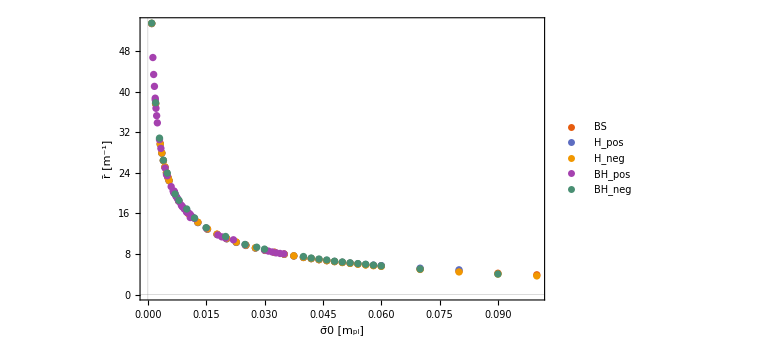

```mathematica
ListPlot[{BS,HX,HXm,BHX,BHXm},PlotTheme->"Scientific",ImageSize->Large,PlotRange->{{0,0.1},All},FrameLabel->{"σ̄0 [m_pl]"," r̄ [m^-1] "},PlotLegends->Placed[{"BS","H_pos", "H_neg", "BH_pos", "BH_neg"},{0.3,0.8}]]
```

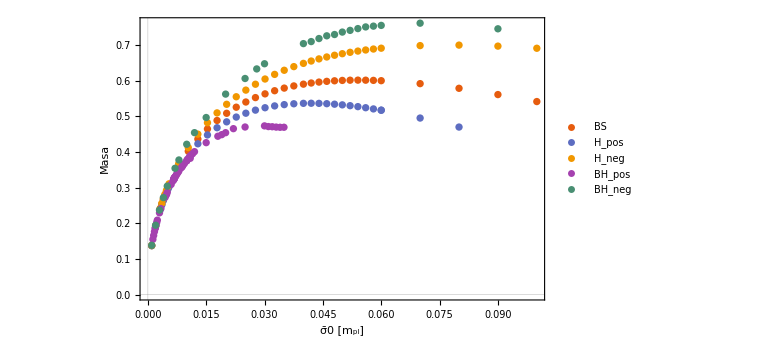

```mathematica
ListPlot[{BSM,HXMasa,HXmMasa, BHXMasa,BHXmMasa},PlotTheme->"Scientific",ImageSize->Large,PlotRange->{{0,0.1},All},FrameLabel->{"σ̄0 [m_pl]"," Masa "},PlotLegends->Placed[{"BS","H_pos", "H_neg","BH_pos", "BH_neg"},{0.3,0.4}]]
```